# ΚΑΤΑΣΚΕΥH ΑΝΑΛΥΣΗ ΚΑΙ ΣΥΓΚΡΙΤΙΚΟΣ ΕΛΕΓΧΟΣ ΑΠOΔΟΣΗ ΜΕΤΟΧΙΚΟΥ ΧΑΡΤΟΦΥΛΑΚΙΟΥ ΠΟΥ ΕΠΕΝΔΥΕΙ ΣΤΟ ΕΛΛΗΝΙΚΟ ΧΡΗΜΑΤΙΣΤΗΡΙΟ

```mathematica
Remove["Global`*"]
```

```mathematica
Statistics
```

```mathematica
date={"17/9/18","18/9/18","19/9/18","20/9/18","21/9/18","24/9/18","25/9/18","26/9/18","27/9/18","28/9/18","1/10/18","2/10/18","3/10/18","4/10/18","5/10/18","8/10/18","9/10/18","10/10/18","11/10/18","12/10/18","15/10/18","16/10/18","17/10/18","18/10/18","19/10/18","22/10/18","23/10/18","24/10/18","25/10/18","26/10/18","29/10/18","30/10/18","31/10/18","1/11/18","2/11/18","5/11/18","6/11/18","7/11/18","8/11/18","9/11/18","12/11/18","13/11/18","14/11/18","15/11/18","16/11/18","19/11/18","20/11/18","21/11/18","22/11/18","23/11/18","26/11/18","27/11/18","28/11/18","29/11/18","30/11/18","3/12/18","4/12/18","5/12/18","6/12/18","7/12/18","10/12/18","11/12/18","12/12/18","13/12/18","14/12/18","17/12/18","18/12/18","19/12/18","20/12/18","21/12/18","27/12/18","28/12/18","31/12/18","2/1/19","3/1/19","4/1/19","7/1/19","8/1/19","9/1/19","10/1/19","11/1/19","14/1/19","15/1/19","16/1/19","17/1/19","18/1/19","21/1/19","22/1/19","23/1/19","24/1/19","25/1/19","28/1/19","29/1/19","30/1/19","31/1/19","1/2/19","4/2/19","5/2/19","6/2/19","7/2/19","8/2/19","11/2/19","12/2/19","13/2/19","14/2/19","15/2/19","18/2/19"};
```

```mathematica
p ={{1.78,2.18,0.452,682.75},{1.79,2.18,0.452,686.68},{1.78,2.18,0.496,689.59},{1.7,2.16,0.496,681.03},{1.72,2.16,0.468,698.74},{1.68,2.12,0.468,689.96},{1.77,2.12,0.468,699.89},{1.75,2.1,0.49,701.89},{1.79,2.06,0.49,707.92},{1.75,2.1,0.49,691.69},{1.73,2.06,0.49,691.3},{1.68,2.02,0.49,681.17},{1.58,2.02,0.49,666.84},{1.73,2.02,0.48,676.36},{1.68,2.06,0.48,658.97},{1.6,2.04,0.48,641.79},{1.54,2.04,0.48,626.17},{1.48,2.04,0.47,625.83},{1.57,2.04,0.47,626.86},{1.54,2.02,0.47,628.33},{1.5,2.02,0.47,634.47},{1.54,2.02,0.47,644.66},{1.52,2.02,0.47,637.08},{1.46,2.02,0.47,631.88},{1.43,2.02,0.47,624.81},{1.4,2.02,0.47,626.61},{1.4,2.02,0.47,619.47},{1.51,2.02,0.482,632.56},{1.51,2.02,0.482,633.46},{1.46,2.,0.482,633.27},{1.5,2.04,0.482,640.07},{1.49,2.04,0.482,636.65},{1.53,2.02,0.482,640.15},{1.49,1.96,0.48,619.32},{1.39,1.96,0.48,619.4},{1.37,1.96,0.48,618.84},{1.39,1.98,0.48,629.84},{1.42,1.98,0.48,640.75},{1.43,1.99,0.47,640.67},{1.39,1.99,0.47,643.42},{1.32,1.98,0.454,635.2},{1.39,2.,0.454,644.},{1.21,2.06,0.442,634.64},{1.14,2.06,0.442,630.59},{1.11,2.06,0.442,625.69},{1.05,2.06,0.442,617.18},{1.,2.06,0.424,593.05},{1.01,1.98,0.424,599.95},{1.02,2.,0.424,598.73},{1.05,1.93,0.44,602.6},{1.02,1.95,0.44,603.43},{0.93,1.97,0.446,604.26},{0.95,1.97,0.446,603.11},{0.99,1.98,0.446,618.16},{1.02,1.96,0.428,630.23},{1.18,2.02,0.42,659.72},{1.15,2.02,0.42,656.96},{1.16,2.02,0.412,656.92},{1.16,2.02,0.412,652.04},{1.14,2.02,0.452,648.71},{1.12,2.02,0.432,638.2},{1.13,2.06,0.432,635.84},{1.16,2.08,0.426,646.16},{1.18,2.08,0.426,648.49},{1.16,2.08,0.426,645.24},{1.15,2.1,0.428,632.04},{1.1,2.1,0.43,625.31},{1.06,2.1,0.42,618.98},{1.03,2.1,0.42,613.5},{1.05,2.06,0.42,608.58},{0.996,2.16,0.408,597.83},{1.05,2.2,0.408,603.84},{1.1,2.2,0.408,613.3},{1.07,2.2,0.408,605.34},{1.05,2.16,0.408,607.05},{1.06,2.2,0.41,615.69},{1.07,2.22,0.41,620.6},{1.11,2.22,0.426,626.13},{1.2,2.22,0.426,638.22},{1.18,2.22,0.424,633.2},{1.14,2.2,0.424,635.7},{1.08,2.24,0.448,629.88},{1.,2.24,0.492,622.78},{1.,2.24,0.53,622.76},{0.958,2.34,0.55,616.96},{0.95,2.28,0.5,617.37},{0.92,2.26,0.55,619.27},{0.965,2.3,0.55,630.17},{0.964,2.3,0.55,631.32},{0.965,2.38,0.55,632.34},{0.96,2.38,0.54,633.32},{0.96,2.38,0.575,630.7},{0.97,2.4,0.575,635.51},{0.968,2.4,0.555,635.67},{0.978,2.4,0.555,634.64},{1.,2.4,0.57,641.48},{1.03,2.42,0.59,647.19},{1.06,2.42,0.585,652.71},{1.08,2.4,0.585,654.39},{1.07,2.42,0.6,645.16},{1.07,2.42,0.595,649.87},{1.1,2.42,0.59,654.57},{1.11,2.4,0.59,655.09},{1.1,2.4,0.605,656.08},{1.08,2.42,0.565,654.03},{1.12,2.42,0.6,655.1},{1.23,2.42,0.6,667.46}};(*107X4*)(*Daily Stock Prices*)
```

```mathematica
r=Table[p[[time,stock]]/p[[time-1,stock]]-1,{time,2,107,1},{stock,1,4,1}];(*106X4*)(*Daily Revenues*)
```

```mathematica
DAILY VALUES
```

```mathematica
meanday=Table[{Mean[r[[All,Stocks]]]},{Stocks,1,4}];(*4X1*)(*Daily Average Revenues*)
```

```mathematica
varday = Table[{Variance[r[[All,Stocks]]]},{Stocks,1,4}];(*4X1*)(*Daily Variance*)
```

```mathematica
stdday= Table[{StandardDeviation[r[[All,Stocks]]]},{Stocks,1,4}];(*4X1*)(*Daily Standar Deviation*)
```

```mathematica
daystat:=Table[{meanday[[i,1]],varday[[i,1]],stdday[[i,1]]},{i,1,4,1}];(*4X3*)
```

```mathematica
YEARLY VALUES
```

```mathematica
meanyear =Table[{Mean[365*r[[All,Stocks]]]},{Stocks,1,4}];(*4X1*)(*Yearly Mean Revenue*)
```

```mathematica
varyear =Table[{365*Variance[r[[All,Stocks]]]},{Stocks,1,4}];(*4X1*)(*Yearly Variance*)
```

```mathematica
stdyear = Table[{Sqrt[365]*StandardDeviation[r[[All,Stocks]]]},{Stocks,1,4}];(*4X1*)(*Yearly Standar Deviation*)
```

```mathematica
yearstat := Table[{meanyear[[i,1]],varday[[i,1]],stdday[[i,1]]},{i,1,4,1}];(*4X3*)
```

```mathematica
MORE STATISTICS
```

```mathematica
cov = Table[{Covariance[r[[All,i]],r[[All,i+1]]],Covariance[r[[All,i]],r[[All,i+2]]],Covariance[r[[All,i+2]],r[[All,i+3]]]},{i,1}];(*1X3*)(*Covariance between Stocks*)
```

```mathematica
cor = Table[{Correlation[r[[All,i]],r[[All,i+1]]],Correlation[r[[All,i]],r[[All,i+2]]],Correlation[r[[All,i+1]],r[[All,i+2]]]},{i,1}];(*1X3*)(*Correlation between Stocks*)
```

```mathematica
relations:= Table[{cov[[1,i]],cor[[1,i]]},{i,1,3}];(*2X3*)
```

```mathematica
covmarket= Table[{Covariance[r[[All,i]],r[[All,i+3]]],Covariance[r[[All,i+1]],r[[All,i+3]]],Covariance[r[[All,i+2]],r[[All,i+3]]]},{i,1}];(*1X3*)(*Covariance between Stocks and market*)
```

```mathematica
cormarket =Table[{Correlation[r[[All,i]],r[[All,i+3]]],Correlation[r[[All,i+1]],r[[All,i+3]]],Correlation[r[[All,i+2]],r[[All,i+3]]]},{i,1}];(*1X3*)(*Covariance between Stocks and market*)
```

```mathematica
relationsmarket:= Table[{covmarket[[1,i]],cormarket[[1,i]]},{i,1,3}];(*2X3*)
```

```mathematica
VarCovar Matrix
```

```mathematica
meanreturn ={{meanday[[1,1]],meanday[[2,1]],meanday[[3,1]]}};(*1X3*)(*horizontal*)(*Mean Return*)
```

```mathematica
exreturn=Table[r[[i,j]]-meanreturn[[1,j]],{i,1,106},{j,1,3}];(*vertical, 106Χ3*)(*Excess Return*)
```

```mathematica
varcovar={{Flatten[exreturn.Transpose[exreturn]/106][[1]],Flatten[exreturn.Transpose[exreturn]/106][[2]],Flatten[exreturn.Transpose[exreturn]/106][[3]]},{Flatten[exreturn.Transpose[exreturn]/106][[1+106]],Flatten[exreturn.Transpose[exreturn]/106][[2+106]],Flatten[exreturn.Transpose[exreturn]/106][[3+106]]},{Flatten[exreturn.Transpose[exreturn]/106][[1+2*106]],Flatten[exreturn.Transpose[exreturn]/106][[2+2*106]],Flatten[exreturn.Transpose[exreturn]/106][[3+2*106]]}};(*3Χ3 Varriance Covarriance Matrix*)
```

```mathematica
weights = {{0.4,0.4,0.2}};(*1X3*)(*ΟΡΙΖΟΝΤΙΟΣ*)(*Σταθμίσεις: προκύπτουν σύμφωνα με την ανέχεια του επενδυτή στον κίνδυνο, αν είναι Risk Lover η στάθμιση της μετοχής με το μεγαλύτερο κίνδυνο θα είναι μεγαλύτερη, ενώ αν ειναι Risk Averse η στάθμιση της μετοχής με το μεγαλύτερο κίνδυνο θα είναι μικρότερη. Παρόμοια προκύπτει και για όλες τις ενδιάμεσες καταστάσεις. Το επενδυτικό προφίλ στη παρούσα κατάσταση είναι του επενδυτή Moderate*)
```

```mathematica
ER= Table[{meanreturn[[1,i]]*weights[[1,i]]},{i,1,3}];(*3X1*)(*ΚΑΘΕΤΟΣ*)(*Stocks Estimated Returns*)
```

```mathematica
ERPort = Sum[ER[[i,1]],{i,1,3}];(*Portfolio Estimated Return*)
```

```mathematica
totalreturns:= {{ER[[1,1]]},{ER[[2,1]]},{ER[[3,1]]},{ERPort}};(*ο συγκεκριμένος πίνακας θα χρησιμοποιηθεί μόνο για visualized αποτελέσματα στο τέλος του NoteBook*)
```

```mathematica
varport = weights.varcovar.Transpose[weights];(*Portfolio's Varriance*)
```

```mathematica
stdport =Sqrt[varport[[1,1]]];(*Portfolio's Standard Deviation*)
```

```mathematica
portstat :={{varport[[1,1]],stdport}};(*Portfolio's Statistic Matrix*)
```

```mathematica
stockbeta = Table[covmarket[[1,i]]/varday[[4]],{i,1,3}];(*ο τύπος για τον υπολογισμό των beta ειναι covariance[stock/market]/variance[market]*);
```

```mathematica
marketbeta = varday[[4]]/varday[[4]];
```

```mathematica
portbeta =Sum[stockbeta[[i]]*weights[[1,i]],{i,1,3}];(*ενώ του Port είναι το άθροισμα των γινομένων των beta με τις σταθμίσεις*)
```

```mathematica
stockalpha:={{meanday[[1]]-stockbeta[[1]]*meanday[[4]]},{meanday[[2]]-stockbeta[[2]]*meanday[[4]]},{meanday[[3]]-stockbeta[[3]]*meanday[[4]]}};(*τα έχω κανει και με Table αλλα πάλι δε λειτουργεί*)
```

```mathematica
Efficient Frontier
```

```mathematica
varportef = {{w1,w2,w3}}.varcovar.{{w1},{w2},{w3}};
```

```mathematica
λ=  Table[x,{x,0,0.0195,0.0005}];
```

```mathematica
a =Table[Simplify[varportef - λ[[i]]*{{w1,w2,w3}}.Transpose[meanreturn]],{i,1,40,1}];
```

```mathematica
Flatten[a][[1]];
```

```mathematica
results=Table[NMinimize[{Flatten[a[[i]]][[1]],w1≥0,w2≥0,w3≥0,w1+w2+w3==1},{w1,w2,w3}],{i,1,40,1}];(*μέχρι εδώ γίνεται ο υπολογισμός των σταθμίσεων για διαφορετικά λ*)
```

```mathematica
temp= Table[{results[[i,1]],w1/.results[[i,2]],w2/.results[[i,2]],w3/.results[[i,2]]},{i,1,40,1}];(*αυτή η συναρτηση βγάζει τα αποτελέσματα των σταθμίσεων από τα αποτελέσματα και τα βάζει σε πίνακα*)
```

```mathematica
results = temp;
```

```mathematica
temp =Table[If[results[[i,2]]<0.009,results[[i,2]]=0],{i,1,40}];(*παρατηρήθηκε πως παρόλο που παραπανω έχω βάλει περιορισμό, ότι συνέχιζαν να υπάρχουν τιμές μικρότερες του μηδενός στη σταθμιση w1 αλλα ήταν της μορφής 10^(-9), επομένως έπρεπε να τις κόψω από τον πίνακα-ελέγχθηκαν επίσης και οι υπόλοιπες σταθμίσεις*)
```

```mathematica
temp=Table[{results[[i,1]], results[[i,1]]+λ[[i]]*(results[[i,2]]*meanreturn[[1,1]]+results[[i,3]]*meanreturn[[1,2]]+results[[i,4]]*meanreturn[[1,3]]),Sqrt[results[[i,1]]+λ[[i]]*(results[[i,2]]*meanreturn[[1,1]]+results[[i,3]]*meanreturn[[1,2]]+results[[i,4]]*meanreturn[[1,3]])],λ[[i]],results[[i,2]]*meanreturn[[1,1]]+results[[i,3]]*meanreturn[[1,2]]+results[[i,4]]*meanreturn[[1,3]],results[[i,2]],results[[i,3]],results[[i,4]],(results[[i,2]]*meanreturn[[1,1]]+results[[i,3]]*meanreturn[[1,2]]+results[[i,4]]*meanreturn[[1,3]])/Sqrt[results[[i,1]]+λ[[i]]*(results[[i,2]]*meanreturn[[1,1]]+results[[i,3]]*meanreturn[[1,2]]+results[[i,4]]*meanreturn[[1,3]])]},{i,1,40}];
```

```mathematica
results=temp;
```

```mathematica
s =2;
```

```mathematica
temp =While[results[[s,9]]>results[[s-1,9]],s=s+1];s=s-1;Print["A/A = ",s];
```

```mathematica
Clear[temp,varportef,λ,a]
```

```mathematica
mvpweights = {{results[[1,6]],results[[1,7]],results[[1,8]],results[[1,5]]}};
```

```mathematica
msrpweights ={{results[[22,6]],results[[22,7]],results[[22,8]],results[[22,5]]}};
```

```mathematica
y[x_,rf_]:=(0.748349837081625-rf)*x-rf
```

```mathematica
Manipulate[Plot[y[x,rf],{x,0,0.06}],{rf,0,1,0.1}],Show[ListLinePlot[Tooltip[Table[{results[[i,3]],results[[i,5]]},{i,1,40}],"Efficient Frontier"]]]
```

```mathematica
Clear[y]
```

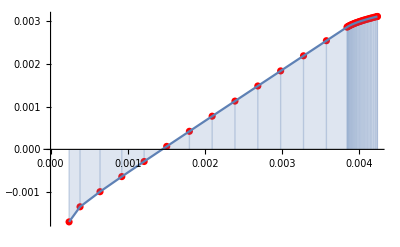

```mathematica
Show[ListPlot[Style[Tooltip[Transpose[{results[[All,3]],results[[All,5]]}],"Efficient Frontier"],Red],Mesh->All,AxesOrigin->{0,0},Filling->Axis,FrameStyle->Directive[Thickness[Tiny]]],ListLinePlot[Tooltip[Transpose[{results[[All,3]],results[[All,5]]}],"Efficient Frontier"],Filling->Axis]]
```

```mathematica
Manipulate[Plot[Tooltip[rf+(0.748349837081625-rf/0.00392718765257293)*x,"CML"],{x,0,0.005},PlotRange-> {{0,0.006},{0,0.006}},PlotStyle->{Dashing[0.01],Red},PlotLabels->{"CML",Automatic},Epilog->{PointSize[0.03],Green,Point[{0.00392718765257293,0.00293891023999192}]}],{{rf,0,"Risk Free Ratio"},0,0.05,0.00001},Button["Reset",rf=0]]
```

```mathematica
Ratios
```

```mathematica
rf =0;
```

```mathematica
ratios:= {{meanday[[1,1]],meanday[[2,1]],meanday[[3,1]],meanday[[4,1]],ERPort},{stockbeta[[1,1]],stockbeta[[2,1]],stockbeta[[3,1]],marketbeta[[1]],portbeta[[1]]},{stdday[[1,1]],stdday[[2,1]],stdday[[3,1]],stdday[[4,1]],portbeta[[1]]*stdday[[4,1]]},{weights[[1,1]],weights[[1,2]],weights[[1,3]],0,0},{(meanday[[1,1]]-rf)/stdday[[1,1]],(meanday[[2,1]]-rf)/stdday[[2,1]],(meanday[[3,1]]-rf)/stdday[[3,1]],(meanday[[4,1]]-rf)/stdday[[4,1]],(ERPort-rf)*portbeta[[1]]/stdday[[4,1]]},{(meanday[[1,1]]-rf)/stockbeta[[1,1]],(meanday[[2,1]]-rf)/stockbeta[[2,1]],(meanday[[3,1]]-rf)/stockbeta[[3,1]],(meanday[[4,1]]-rf)/marketbeta[[1]],(ERPort-rf)/portbeta[[1]]},{meanday[[1,1]]-(rf+stockbeta[[1,1]]*(meanday[[4,1]]-rf)),meanday[[2,1]]-(rf+stockbeta[[2,1]]*(meanday[[4,1]]-rf)),meanday[[3,1]]-(rf+stockbeta[[3,1]]*(meanday[[4,1]]-rf)),meanday[[4,1]]-(rf+marketbeta[[1]]*(meanday[[4,1]]-rf)),ERPort-(rf+portbeta[[1]]*(meanday[[4,1]]-rf))}};
```

```mathematica
Technical Analysis
```

```mathematica
MA10NBG = Transpose[{Flatten[{"-","-","-","-","-","-","-","-","-",MovingAverage[p[[All,1]],10]}]}];
```

```mathematica
MA25NBG = Transpose[{Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",MovingAverage[p[[All,1]],25]}]}];
```

```mathematica
signsMANBG=Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[If[MA10NBG[[i,1]]>MA25NBG[[i,1]]&&MA10NBG[[i-1,1]]<MA25NBG[[i-1,1]],"BUY",If[MA10NBG[[i,1]]<MA25NBG[[i,1]]&&MA10NBG[[i-1,1]]>MA25NBG[[i-1,1]],"SELL","-"]],{i,26,107}]}];
```

```mathematica
MA10LOULI =  Transpose[{Flatten[{"-","-","-","-","-","-","-","-","-",MovingAverage[p[[All,2]],10]}]}];
```

```mathematica
MA25LOULI =Transpose[{Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",MovingAverage[p[[All,2]],25]}]}];
```

```mathematica
signsMALOULI=Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[If[MA10LOULI[[i,1]]>MA25LOULI[[i,1]]&&MA10LOULI[[i-1,1]]<MA25LOULI[[i-1,1]],"BUY",If[MA10LOULI[[i,1]]<MA25LOULI[[i,1]]&&MA10LOULI[[i-1,1]]>MA25LOULI[[i-1,1]],"SELL","-"]],{i,26,107}]}];
```

```mathematica
MA10REVOIL =  Transpose[{Flatten[{"-","-","-","-","-","-","-","-","-",MovingAverage[p[[All,3]],10]}]}];
```

```mathematica
MA25REVOIL = Transpose[{Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",MovingAverage[p[[All,3]],25]}]}];
```

```mathematica
signsMAREVOIL=Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[If[MA10REVOIL[[i,1]]>MA25REVOIL[[i,1]]&&MA10REVOIL[[i-1,1]]<MA25REVOIL[[i-1,1]],"BUY",If[MA10REVOIL[[i,1]]<MA25REVOIL[[i,1]]&&MA10REVOIL[[i-1,1]]>MA25REVOIL[[i-1,1]],"SELL","-"]],{i,26,107}]}];
```

```mathematica
variationNBG = Flatten[{"0",Table[p[[i,1]]-p[[i-1,1]],{i,2,107}]}];
```

```mathematica
profitNBG = Table[If[variationNBG[[i]]>0,variationNBG[[i]],0],{i,1,107}];
```

```mathematica
loseNBG = Table[If[variationNBG[[i]]<0,-variationNBG[[i]],0],{i,1,107}];
```

```mathematica
meanprofitNBG =Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[(Sum[profitNBG[[i]],{i,j,j+13}])/14,{j,2,94}]}];
```

```mathematica
meanloseNBG =Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[(Sum[loseNBG[[i]],{i,j,j+13}])/14,{j,2,94}]}];
```

```mathematica
RSNBG = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[meanprofitNBG[[i]]/meanloseNBG[[i]],{i,15,107}]}];
```

```mathematica
RSI14NBG = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[100-(100/(1+RSNBG[[i]])),{i,15,107}]}];
```

```mathematica
signsRSI14NBG = Table[If[RSI14NBG[[i]]>30&&RSI14NBG[[i-1]]<30&&RSI14NBG[[i]]≠ "-"&&RSI14NBG[[i-1]]≠ "-","BUY",If[RSI14NBG[[i]]<70&&RSI14NBG[[i-1]]>70&&RSI14NBG[[i]]≠ "-"&&RSI14NBG[[i-1]]≠ "-","SELL","-"]],{i,1,107}];
```

```mathematica
variationLOULI = Flatten[{"0",Table[p[[i,2]]-p[[i-1,2]],{i,2,107}]}];
```

```mathematica
profitLOULI = Table[If[variationLOULI[[i]]>0,variationLOULI[[i]],0],{i,1,107}];
```

```mathematica
loseLOULI= Table[If[variationLOULI[[i]]<0,-variationLOULI[[i]],0],{i,1,107}];
```

```mathematica
meanprofitLOULI =Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[(Sum[profitLOULI[[i]],{i,j,j+13}])/14,{j,2,94}]}];
```

```mathematica
meanloseLOULI =Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[(Sum[loseLOULI[[i]],{i,j,j+13}])/14,{j,2,94}]}];
```

```mathematica
RSLOULI = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[meanprofitLOULI[[i]]/meanloseLOULI[[i]],{i,15,107}]}];
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
RSI14LOULI = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[100-(100/(1+RSLOULI[[i]])),{i,15,107}]}];
```

```mathematica
signsRSI14LOULI = Table[If[RSI14LOULI[[i]]>30&&RSI14LOULI[[i-1]]<30&&RSI14LOULI[[i]]≠ "-"&&RSI14LOULI[[i-1]]≠ "-","BUY",If[RSI14LOULI[[i]]<70&&RSI14LOULI[[i-1]]>70&&RSI14LOULI[[i]]≠ "-"&&RSI14LOULI[[i-1]]≠ "-","SELL","-"]],{i,1,107}];
```

```mathematica
variationREVOIL = Flatten[{"0",Table[p[[i,3]]-p[[i-1,3]],{i,2,107}]}];
```

```mathematica
profitREVOIL = Table[If[variationREVOIL[[i]]>0,variationREVOIL[[i]],0],{i,1,107}];
```

```mathematica
loseREVOIL= Table[If[variationREVOIL[[i]]<0,-variationREVOIL[[i]],0],{i,1,107}];
```

```mathematica
meanprofitREVOIL =Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[(Sum[profitREVOIL[[i]],{i,j,j+13}])/14,{j,2,94}]}];
```

```mathematica
meanloseREVOIL =Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[(Sum[loseREVOIL[[i]],{i,j,j+13}])/14,{j,2,94}]}];
```

```mathematica
RSREVOIL = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[meanprofitREVOIL[[i]]/meanloseREVOIL[[i]],{i,15,107}]}];
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
RSI14REVOIL= Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[100-(100/(1+RSREVOIL[[i]])),{i,15,107}]}];
```

```mathematica
signsRSI14REVOIL= Table[If[RSI14REVOIL[[i]]>30&&RSI14REVOIL[[i-1]]<30&&RSI14REVOIL[[i]]≠ "-"&&RSI14REVOIL[[i-1]]≠ "-","BUY",If[RSI14REVOIL[[i]]<70&&RSI14REVOIL[[i-1]]>70&&RSI14REVOIL[[i]]≠ "-"&&RSI14REVOIL[[i-1]]≠ "-","SELL","-"]],{i,1,107}];
```

```mathematica
variationNBG = Flatten[{"-",Table[p[[i,1]]-p[[i-1,1]],{i,2,107}]}];profitNBG = Flatten[{"-",Table[If[variationNBG[[i]]>0,variationNBG[[i]],"-"],{i,2,107}]}];loseNBG = Flatten[{"-",Table[If[variationNBG[[i]]<0,-variationNBG[[i]],"-"],{i,2,107}]}];variationLOULI = Flatten[{"-",Table[p[[i,2]]-p[[i-1,2]],{i,2,107}]}];profitLOULI = Flatten[{"-",Table[If[variationLOULI[[i]]>0,variationLOULI[[i]],"-"],{i,2,107}]}];loseLOULI = Flatten[{"-",Table[If[variationLOULI[[i]]<0,-variationLOULI[[i]],"-"],{i,2,107}]}];variationREVOIL= Flatten[{"-",Table[p[[i,3]]-p[[i-1,3]],{i,2,107}]}];profitREVOIL= Flatten[{"-",Table[If[variationREVOIL[[i]]>0,variationREVOIL[[i]],"-"],{i,2,107}]}];loseREVOIL = Flatten[{"-",Table[If[variationREVOIL[[i]]<0,-variationREVOIL[[i]],"-"],{i,2,107}]}];
```

```mathematica
EMA12NBG = Flatten[{"-","-","-","-","-","-","-","-","-","-","-",ExponentialMovingAverage[Flatten[{{Sum[p[[i,1]],{i,1,12}]/12,Table[p[[i,1]],{i,13,107}]}}],2/13]}];
```

```mathematica
EMA26NBG = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",ExponentialMovingAverage[Flatten[{{Sum[p[[i,1]],{i,1,26}]/26,Table[p[[i,1]],{i,27,107}]}}],2/27]}];
```

```mathematica
MACDNBG =  Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[EMA12NBG[[i]]-EMA26NBG[[i]],{i,26,107}]}];
```

```mathematica
EMA9SIGNALLINENBG = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",ExponentialMovingAverage[Flatten[{{Sum[MACDNBG[[i]],{i,26,34}]/9,Table[MACDNBG[[i]],{i,35,107}]}}],2/10]}];
```

```mathematica
HISTOGRAMNBG = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[MACDNBG[[i]]-EMA9SIGNALLINENBG[[i]],{i,34,107}]}];
```

```mathematica
signsMACDNBG= Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[If[MACDNBG[[i-1]]<0&&MACDNBG[[i-1]]<EMA9SIGNALLINENBG[[i-1]]&&MACDNBG[[i]]>EMA9SIGNALLINENBG[[i]]&&EMA9SIGNALLINENBG[[i-1]]≠"-","BUY",If[MACDNBG[[i-1]]>0&&MACDNBG[[i-1]]>EMA9SIGNALLINENBG[[i-1]]&&MACDNBG[[i]]<EMA9SIGNALLINENBG[[i]]&&EMA9SIGNALLINENBG[[i-1]]≠"-","SELL","-"]],{i,34,107}]}];
```

```mathematica
EMA12LOULI = Flatten[{"-","-","-","-","-","-","-","-","-","-","-",ExponentialMovingAverage[Flatten[{{Sum[p[[i,2]],{i,1,12}]/12,Table[p[[i,2]],{i,13,107}]}}],2/13]}];
```

```mathematica
EMA26LOULI = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",ExponentialMovingAverage[Flatten[{{Sum[p[[i,2]],{i,1,26}]/26,Table[p[[i,2]],{i,27,107}]}}],2/27]}];
```

```mathematica
MACDLOULI=  Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[EMA12LOULI[[i]]-EMA26LOULI[[i]],{i,26,107}]}];
```

```mathematica
EMA9SIGNALLINELOULI = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",ExponentialMovingAverage[Flatten[{{Sum[MACDLOULI[[i]],{i,26,34}]/9,Table[MACDLOULI[[i]],{i,35,107}]}}],2/10]}];
```

```mathematica
HISTOGRAMLOULI = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[MACDLOULI[[i]]-EMA9SIGNALLINELOULI[[i]],{i,34,107}]}];
```

```mathematica
signsMACDLOULI= Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[If[MACDLOULI[[i-1]]<0&&MACDLOULI[[i-1]]<EMA9SIGNALLINELOULI[[i-1]]&&MACDLOULI[[i]]>EMA9SIGNALLINELOULI[[i]]&&EMA9SIGNALLINELOULI[[i-1]]≠"-","BUY",If[MACDLOULI[[i-1]]>0&&MACDLOULI[[i-1]]>EMA9SIGNALLINELOULI[[i-1]]&&MACDLOULI[[i]]<EMA9SIGNALLINELOULI[[i]]&&EMA9SIGNALLINELOULI[[i-1]]≠"-","SELL","-"]],{i,34,107}]}];
```

```mathematica
EMA12REVOIL= Flatten[{"-","-","-","-","-","-","-","-","-","-","-",ExponentialMovingAverage[Flatten[{{Sum[p[[i,3]],{i,1,12}]/12,Table[p[[i,3]],{i,13,107}]}}],2/13]}];
```

```mathematica
EMA26REVOIL = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",ExponentialMovingAverage[Flatten[{{Sum[p[[i,3]],{i,1,26}]/26,Table[p[[i,3]],{i,27,107}]}}],2/27]}];
```

```mathematica
MACDREVOIL=  Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[EMA12REVOIL[[i]]-EMA26REVOIL[[i]],{i,26,107}]}];
```

```mathematica
EMA9SIGNALLINEREVOIL = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",ExponentialMovingAverage[Flatten[{{Sum[MACDREVOIL[[i]],{i,26,34}]/9,Table[MACDREVOIL[[i]],{i,35,107}]}}],2/10]}];
```

```mathematica
HISTOGRAMREVOIL = Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[MACDREVOIL[[i]]-EMA9SIGNALLINEREVOIL[[i]],{i,34,107}]}];
```

```mathematica
signsMACDREVOIL= Flatten[{"-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-","-",Table[If[MACDREVOIL[[i-1]]<0&&MACDREVOIL[[i-1]]<EMA9SIGNALLINEREVOIL[[i-1]]&&MACDREVOIL[[i]]>EMA9SIGNALLINEREVOIL[[i]]&&EMA9SIGNALLINEREVOIL[[i-1]]≠"-","BUY",If[MACDREVOIL[[i-1]]>0&&MACDREVOIL[[i-1]]>EMA9SIGNALLINEREVOIL[[i-1]]&&MACDREVOIL[[i]]<EMA9SIGNALLINEREVOIL[[i]]&&EMA9SIGNALLINEREVOIL[[i-1]]≠"-","SELL","-"]],{i,34,107}]}];
```

```mathematica
ta = Table[{p[[i,1]],p[[i,2]],p[[i,3]],MA10NBG[[i,1]],MA25NBG[[i,1]],signsMANBG[[i]],MA10LOULI[[i,1]],MA25LOULI[[i,1]],signsMALOULI[[i]],MA10REVOIL[[i,1]],MA25REVOIL[[i,1]],signsMAREVOIL[[i]],variationNBG[[i]],profitNBG[[i]],loseNBG[[i]],meanprofitNBG[[i]],meanloseNBG[[i]],RSNBG[[i]],RSI14NBG[[i]],signsRSI14NBG[[i]],variationLOULI[[i]],profitLOULI[[i]],loseLOULI[[i]],meanprofitLOULI[[i]],meanloseLOULI[[i]],RSLOULI[[i]],RSI14LOULI[[i]],signsRSI14REVOIL[[i]],variationREVOIL[[i]],profitREVOIL[[i]],loseREVOIL[[i]],meanprofitREVOIL[[i]],meanloseREVOIL[[i]],RSREVOIL[[i]],RSI14REVOIL[[i]],signsRSI14REVOIL[[i]],EMA12NBG[[i]],EMA26NBG[[i]],MACDNBG[[i]],EMA9SIGNALLINENBG[[i]],HISTOGRAMNBG[[i]],signsMACDNBG[[i]],EMA12LOULI[[i]],EMA26LOULI[[i]],MACDLOULI[[i]],EMA9SIGNALLINELOULI[[i]],HISTOGRAMLOULI[[i]],signsMACDLOULI[[i]],EMA12REVOIL[[i]],EMA26REVOIL[[i]],MACDREVOIL[[i]],EMA9SIGNALLINEREVOIL[[i]],HISTOGRAMREVOIL[[i]],signsMACDREVOIL[[i]]},{i,1,107}];
```

```mathematica
Criteria for Signs
```

```mathematica
finalbuysignsNBG =Flatten[{"-","-","-","-","-","-","-","-", Table[If[signsMANBG[[i]] == signsRSI14NBG [[i]]== "BUY"||signsMANBG[[i]] ==signsMACDNBG[[i]]== "BUY"|| signsRSI14NBG [[i]]==signsMACDNBG[[i]]=="BUY","BUY",If[(signsMANBG[[i]] == signsMANBG [[i-1]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-1]]≠ "BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsRSI14NBG[[i]] == signsMANBG [[i-1]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-1]]≠ "BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsMACDNBG[[i]] == signsMANBG [[i-1]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsRSI14NBG[[i-1]]≠ "BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsMANBG[[i]] == signsRSI14NBG [[i-1]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsRSI14NBG[[i]] == signsRSI14NBG [[i-1]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsMACDNBG[[i]] == signsRSI14NBG [[i-1]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsMANBG[[i]] == signsMACDNBG [[i-1]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY")||(signsRSI14NBG[[i]] == signsMACDNBG [[i-1]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY")||(signsMACDNBG[[i]] == signsMACDNBG [[i-1]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"),"BUY",If[(signsMANBG[[i]] == signsMANBG [[i-2]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-2]]≠ "BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsRSI14NBG[[i]] == signsMANBG [[i-2]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-2]]≠ "BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsMACDNBG[[i]] == signsMANBG [[i-2]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsRSI14NBG[[i-2]]≠ "BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsMANBG[[i]] == signsRSI14NBG [[i-2]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsRSI14NBG[[i]] == signsRSI14NBG [[i-2]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsMACDNBG[[i]] == signsRSI14NBG [[i-2]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsMANBG[[i]] == signsMACDNBG [[i-2]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsRSI14NBG[[i]] == signsMACDNBG [[i-2]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY")||(signsMACDNBG[[i]] == signsMACDNBG [[i-2]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"),"BUY",If[(signsMANBG[[i]] == signsMANBG [[i-3]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY")||(signsRSI14NBG[[i]] == signsMANBG [[i-3]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY")||(signsMACDNBG[[i]] == signsMANBG [[i-3]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY")||(signsMANBG[[i]] == signsRSI14NBG [[i-3]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY")||(signsRSI14NBG[[i]] == signsRSI14NBG [[i-3]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY")||(signsMACDNBG[[i]] == signsRSI14NBG [[i-3]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY")||(signsMANBG[[i]] == signsMACDNBG [[i-3]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-3]]≠ "BUY"&&signsRSI14NBG[[i-3]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY")||(signsRSI14NBG[[i]] == signsMACDNBG [[i-3]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-3]]≠ "BUY"&&signsRSI14NBG[[i-3]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY")||(signsMACDNBG[[i]] == signsMACDNBG [[i-3]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-3]]≠ "BUY"&&signsRSI14NBG[[i-3]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"),"BUY",If[(signsMANBG[[i]] == signsMANBG [[i-4]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY")||(signsRSI14NBG[[i]] == signsMANBG [[i-4]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY")||(signsMACDNBG[[i]] == signsMANBG [[i-4]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY")||(signsMANBG[[i]] == signsRSI14NBG [[i-4]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY")||(signsRSI14NBG[[i]] == signsRSI14NBG [[i-4]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY")||(signsMACDNBG[[i]] == signsRSI14NBG [[i-4]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY")||(signsMANBG[[i]] == signsMACDNBG [[i-4]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-4]]≠ "BUY"&&signsRSI14NBG[[i-4]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY")||(signsRSI14NBG[[i]] == signsMACDNBG [[i-4]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-4]]≠ "BUY"&&signsRSI14NBG[[i-4]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY")||(signsMACDNBG[[i]] == signsMACDNBG [[i-4]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-4]]≠ "BUY"&&signsRSI14NBG[[i-4]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"),"BUY",If[(signsMANBG[[i]] == signsMANBG [[i-5]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY")||(signsRSI14NBG[[i]] == signsMANBG [[i-5]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY")||(signsMACDNBG[[i]] == signsMANBG [[i-5]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY")||(signsMANBG[[i]] == signsRSI14NBG [[i-5]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY")||(signsRSI14NBG[[i]] == signsRSI14NBG [[i-5]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY")||(signsMACDNBG[[i]] == signsRSI14NBG [[i-5]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY")||(signsMANBG[[i]] == signsMACDNBG [[i-5]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-5]]≠ "BUY"&&signsRSI14NBG[[i-5]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY")||(signsRSI14NBG[[i]] == signsMACDNBG [[i-5]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-5]]≠ "BUY"&&signsRSI14NBG[[i-5]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY")||(signsMACDNBG[[i]] == signsMACDNBG [[i-5]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-5]]≠ "BUY"&&signsRSI14NBG[[i-5]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"),"BUY",If[(signsMANBG[[i]] == signsMANBG [[i-6]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY")||(signsRSI14NBG[[i]] == signsMANBG [[i-6]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY")||(signsMACDNBG[[i]] == signsMANBG [[i-6]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY")||(signsMANBG[[i]] == signsRSI14NBG [[i-6]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY")||(signsRSI14NBG[[i]] == signsRSI14NBG [[i-6]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY")||(signsMACDNBG[[i]] == signsRSI14NBG [[i-6]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY")||(signsMANBG[[i]] == signsMACDNBG [[i-6]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-6]]≠ "BUY"&&signsRSI14NBG[[i-6]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY")||(signsRSI14NBG[[i]] == signsMACDNBG [[i-6]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-6]]≠ "BUY"&&signsRSI14NBG[[i-6]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY")||(signsMACDNBG[[i]] == signsMACDNBG [[i-6]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-6]]≠ "BUY"&&signsRSI14NBG[[i-6]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"),"BUY",If[(signsMANBG[[i]] == signsMANBG [[i-7]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY")||(signsRSI14NBG[[i]] == signsMANBG [[i-7]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY")||(signsMACDNBG[[i]] == signsMANBG [[i-7]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY")||(signsMANBG[[i]] == signsRSI14NBG [[i-7]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY")||(signsRSI14NBG[[i]] == signsRSI14NBG [[i-7]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY")||(signsMACDNBG[[i]] == signsRSI14NBG [[i-7]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY")||(signsMANBG[[i]] == signsMACDNBG [[i-7]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-7]]≠ "BUY"&&signsRSI14NBG[[i-7]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY")||(signsRSI14NBG[[i]] == signsMACDNBG [[i-7]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-7]]≠ "BUY"&&signsRSI14NBG[[i-7]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY")||(signsMACDNBG[[i]] == signsMACDNBG [[i-7]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-7]]≠ "BUY"&&signsRSI14NBG[[i-7]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"),"BUY",If[(signsMANBG[[i]] == signsMANBG [[i-8]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-8]]≠ "BUY"&&signsMACDNBG[[i-8]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-7]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY")||(signsRSI14NBG[[i]] == signsMANBG [[i-8]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsRSI14NBG[[i-8]]≠ "BUY"&&signsMACDNBG[[i-8]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-7]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY")||(signsMACDNBG[[i]] == signsMANBG [[i-8]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsRSI14NBG[[i-8]]≠ "BUY"&&signsMACDNBG[[i-8]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY")||(signsMANBG[[i]] == signsRSI14NBG [[i-8]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-8]]≠ "BUY"&&signsMACDNBG[[i-8]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-7]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY")||(signsRSI14NBG[[i]] == signsRSI14NBG [[i-8]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-8]]≠ "BUY"&&signsMACDNBG[[i-8]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-7]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY")||(signsMACDNBG[[i]] == signsRSI14NBG [[i-8]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-8]]≠ "BUY"&&signsMACDNBG[[i-8]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-7]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY")||(signsMANBG[[i]] == signsMACDNBG [[i-8]]== "BUY"&&signsRSI14NBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-8]]≠ "BUY"&&signsRSI14NBG[[i-8]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-7]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY")||(signsRSI14NBG[[i]] == signsMACDNBG [[i-8]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsMACDNBG[[i]]≠"BUY"&&signsMANBG[[i-8]]≠ "BUY"&&signsRSI14NBG[[i-8]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-7]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY")||(signsMACDNBG[[i]] == signsMACDNBG [[i-8]]== "BUY"&&signsMANBG[[i]]≠ "BUY"&&signsRSI14NBG[[i]]≠"BUY"&&signsMANBG[[i-8]]≠ "BUY"&&signsRSI14NBG[[i-8]]≠"BUY"&&signsMANBG[[i-1]]≠ "BUY"&&signsRSI14NBG[[i-1]]≠"BUY"&&signsMACDNBG[[i-1]]≠"BUY"&&signsMANBG[[i-2]]≠ "BUY"&&signsRSI14NBG[[i-2]]≠"BUY"&&signsMACDNBG[[i-2]]≠"BUY"&&signsMANBG[[i-3]]≠"BUY"&&signsRSI14NBG[[i-3]]≠ "BUY"&&signsMACDNBG[[i-3]]≠"BUY"&&signsMANBG[[i-4]]≠"BUY"&&signsRSI14NBG[[i-4]]≠ "BUY"&&signsMACDNBG[[i-4]]≠"BUY"&&signsMANBG[[i-5]]≠"BUY"&&signsRSI14NBG[[i-5]]≠ "BUY"&&signsMACDNBG[[i-5]]≠"BUY"&&signsMANBG[[i-6]]≠"BUY"&&signsRSI14NBG[[i-6]]≠ "BUY"&&signsMACDNBG[[i-6]]≠"BUY"&&signsMANBG[[i-7]]≠"BUY"&&signsRSI14NBG[[i-7]]≠ "BUY"&&signsMACDNBG[[i-7]]≠"BUY"),"BUY","-"]]]]]]]]],{i,9,107}]}];
```

```mathematica
finalsellsignsNBG=Flatten[{"-","-","-","-","-","-","-","-",Table[If[signsMANBG[[i]]==signsRSI14NBG[[i]]=="SELL"||signsMANBG[[i]]==signsMACDNBG[[i]]=="SELL"||signsRSI14NBG[[i]]==signsMACDNBG[[i]]=="SELL","SELL",If[(signsMANBG[[i]]==signsMANBG[[i-1]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsRSI14NBG[[i]]==signsMANBG[[i-1]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsMACDNBG[[i]]==signsMANBG[[i-1]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsMANBG[[i]]==signsRSI14NBG[[i-1]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsRSI14NBG[[i]]==signsRSI14NBG[[i-1]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsMACDNBG[[i]]==signsRSI14NBG[[i-1]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsMANBG[[i]]==signsMACDNBG[[i-1]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL")||(signsRSI14NBG[[i]]==signsMACDNBG[[i-1]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL")||(signsMACDNBG[[i]]==signsMACDNBG[[i-1]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"),"SELL",If[(signsMANBG[[i]]==signsMANBG[[i-2]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsRSI14NBG[[i]]==signsMANBG[[i-2]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsMACDNBG[[i]]==signsMANBG[[i-2]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsMANBG[[i]]==signsRSI14NBG[[i-2]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsRSI14NBG[[i]]==signsRSI14NBG[[i-2]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsMACDNBG[[i]]==signsRSI14NBG[[i-2]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsMANBG[[i]]==signsMACDNBG[[i-2]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsRSI14NBG[[i]]==signsMACDNBG[[i-2]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL")||(signsMACDNBG[[i]]==signsMACDNBG[[i-2]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"),"SELL",If[(signsMANBG[[i]]==signsMANBG[[i-3]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL")||(signsRSI14NBG[[i]]==signsMANBG[[i-3]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL")||(signsMACDNBG[[i]]==signsMANBG[[i-3]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL")||(signsMANBG[[i]]==signsRSI14NBG[[i-3]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL")||(signsRSI14NBG[[i]]==signsRSI14NBG[[i-3]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL")||(signsMACDNBG[[i]]==signsRSI14NBG[[i-3]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL")||(signsMANBG[[i]]==signsMACDNBG[[i-3]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL")||(signsRSI14NBG[[i]]==signsMACDNBG[[i-3]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL")||(signsMACDNBG[[i]]==signsMACDNBG[[i-3]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"),"SELL",If[(signsMANBG[[i]]==signsMANBG[[i-4]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL")||(signsRSI14NBG[[i]]==signsMANBG[[i-4]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL")||(signsMACDNBG[[i]]==signsMANBG[[i-4]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL")||(signsMANBG[[i]]==signsRSI14NBG[[i-4]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL")||(signsRSI14NBG[[i]]==signsRSI14NBG[[i-4]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL")||(signsMACDNBG[[i]]==signsRSI14NBG[[i-4]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL")||(signsMANBG[[i]]==signsMACDNBG[[i-4]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL")||(signsRSI14NBG[[i]]==signsMACDNBG[[i-4]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL")||(signsMACDNBG[[i]]==signsMACDNBG[[i-4]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"),"SELL",If[(signsMANBG[[i]]==signsMANBG[[i-5]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL")||(signsRSI14NBG[[i]]==signsMANBG[[i-5]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL")||(signsMACDNBG[[i]]==signsMANBG[[i-5]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL")||(signsMANBG[[i]]==signsRSI14NBG[[i-5]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL")||(signsRSI14NBG[[i]]==signsRSI14NBG[[i-5]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL")||(signsMACDNBG[[i]]==signsRSI14NBG[[i-5]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL")||(signsMANBG[[i]]==signsMACDNBG[[i-5]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL")||(signsRSI14NBG[[i]]==signsMACDNBG[[i-5]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL")||(signsMACDNBG[[i]]==signsMACDNBG[[i-5]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"),"SELL",If[(signsMANBG[[i]]==signsMANBG[[i-6]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL")||(signsRSI14NBG[[i]]==signsMANBG[[i-6]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL")||(signsMACDNBG[[i]]==signsMANBG[[i-6]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL")||(signsMANBG[[i]]==signsRSI14NBG[[i-6]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL")||(signsRSI14NBG[[i]]==signsRSI14NBG[[i-6]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL")||(signsMACDNBG[[i]]==signsRSI14NBG[[i-6]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL")||(signsMANBG[[i]]==signsMACDNBG[[i-6]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL")||(signsRSI14NBG[[i]]==signsMACDNBG[[i-6]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL")||(signsMACDNBG[[i]]==signsMACDNBG[[i-6]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"),"SELL",If[(signsMANBG[[i]]==signsMANBG[[i-7]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL")||(signsRSI14NBG[[i]]==signsMANBG[[i-7]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL")||(signsMACDNBG[[i]]==signsMANBG[[i-7]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL")||(signsMANBG[[i]]==signsRSI14NBG[[i-7]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL")||(signsRSI14NBG[[i]]==signsRSI14NBG[[i-7]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL")||(signsMACDNBG[[i]]==signsRSI14NBG[[i-7]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL")||(signsMANBG[[i]]==signsMACDNBG[[i-7]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL")||(signsRSI14NBG[[i]]==signsMACDNBG[[i-7]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL")||(signsMACDNBG[[i]]==signsMACDNBG[[i-7]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"),"SELL",If[(signsMANBG[[i]]==signsMANBG[[i-8]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-8]]≠"SELL"&&signsMACDNBG[[i-8]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL")||(signsRSI14NBG[[i]]==signsMANBG[[i-8]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsRSI14NBG[[i-8]]≠"SELL"&&signsMACDNBG[[i-8]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL")||(signsMACDNBG[[i]]==signsMANBG[[i-8]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsRSI14NBG[[i-8]]≠"SELL"&&signsMACDNBG[[i-8]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL")||(signsMANBG[[i]]==signsRSI14NBG[[i-8]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-8]]≠"SELL"&&signsMACDNBG[[i-8]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL")||(signsRSI14NBG[[i]]==signsRSI14NBG[[i-8]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-8]]≠"SELL"&&signsMACDNBG[[i-8]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL")||(signsMACDNBG[[i]]==signsRSI14NBG[[i-8]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-8]]≠"SELL"&&signsMACDNBG[[i-8]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL")||(signsMANBG[[i]]==signsMACDNBG[[i-8]]=="SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-8]]≠"SELL"&&signsRSI14NBG[[i-8]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL")||(signsRSI14NBG[[i]]==signsMACDNBG[[i-8]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsMACDNBG[[i]]≠"SELL"&&signsMANBG[[i-8]]≠"SELL"&&signsRSI14NBG[[i-8]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL")||(signsMACDNBG[[i]]==signsMACDNBG[[i-8]]=="SELL"&&signsMANBG[[i]]≠"SELL"&&signsRSI14NBG[[i]]≠"SELL"&&signsMANBG[[i-8]]≠"SELL"&&signsRSI14NBG[[i-8]]≠"SELL"&&signsMANBG[[i-1]]≠"SELL"&&signsRSI14NBG[[i-1]]≠"SELL"&&signsMACDNBG[[i-1]]≠"SELL"&&signsMANBG[[i-2]]≠"SELL"&&signsRSI14NBG[[i-2]]≠"SELL"&&signsMACDNBG[[i-2]]≠"SELL"&&signsMANBG[[i-3]]≠"SELL"&&signsRSI14NBG[[i-3]]≠"SELL"&&signsMACDNBG[[i-3]]≠"SELL"&&signsMANBG[[i-4]]≠"SELL"&&signsRSI14NBG[[i-4]]≠"SELL"&&signsMACDNBG[[i-4]]≠"SELL"&&signsMANBG[[i-5]]≠"SELL"&&signsRSI14NBG[[i-5]]≠"SELL"&&signsMACDNBG[[i-5]]≠"SELL"&&signsMANBG[[i-6]]≠"SELL"&&signsRSI14NBG[[i-6]]≠"SELL"&&signsMACDNBG[[i-6]]≠"SELL"&&signsMANBG[[i-7]]≠"SELL"&&signsRSI14NBG[[i-7]]≠"SELL"&&signsMACDNBG[[i-7]]≠"SELL"),"SELL","-"]]]]]]]]],{i,9,107}]}];
```

```mathematica
finalbuysignsLOULI=Flatten[{"-","-","-","-","-","-","-","-",Table[If[signsMALOULI[[i]]==signsRSI14LOULI[[i]]=="BUY"||signsMALOULI[[i]]==signsMACDLOULI[[i]]=="BUY"||signsRSI14LOULI[[i]]==signsMACDLOULI[[i]]=="BUY","BUY",If[(signsMALOULI[[i]]==signsMALOULI[[i-1]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-1]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsMACDLOULI[[i]]==signsMALOULI[[i-1]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-1]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-1]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-1]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsMALOULI[[i]]==signsMACDLOULI[[i-1]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-1]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-1]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"),"BUY",If[(signsMALOULI[[i]]==signsMALOULI[[i-2]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-2]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsMACDLOULI[[i]]==signsMALOULI[[i-2]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-2]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-2]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-2]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsMALOULI[[i]]==signsMACDLOULI[[i-2]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-2]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-2]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"),"BUY",If[(signsMALOULI[[i]]==signsMALOULI[[i-3]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-3]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY")||(signsMACDLOULI[[i]]==signsMALOULI[[i-3]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-3]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-3]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-3]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY")||(signsMALOULI[[i]]==signsMACDLOULI[[i-3]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-3]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-3]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"),"BUY",If[(signsMALOULI[[i]]==signsMALOULI[[i-4]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-4]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY")||(signsMACDLOULI[[i]]==signsMALOULI[[i-4]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-4]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-4]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-4]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY")||(signsMALOULI[[i]]==signsMACDLOULI[[i-4]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-4]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-4]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"),"BUY",If[(signsMALOULI[[i]]==signsMALOULI[[i-5]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-5]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY")||(signsMACDLOULI[[i]]==signsMALOULI[[i-5]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-5]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-5]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-5]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY")||(signsMALOULI[[i]]==signsMACDLOULI[[i-5]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-5]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-5]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"),"BUY",If[(signsMALOULI[[i]]==signsMALOULI[[i-6]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-6]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY")||(signsMACDLOULI[[i]]==signsMALOULI[[i-6]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-6]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-6]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-6]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY")||(signsMALOULI[[i]]==signsMACDLOULI[[i-6]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-6]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-6]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"),"BUY",If[(signsMALOULI[[i]]==signsMALOULI[[i-7]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-7]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY")||(signsMACDLOULI[[i]]==signsMALOULI[[i-7]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-7]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-7]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-7]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY")||(signsMALOULI[[i]]==signsMACDLOULI[[i-7]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-7]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-7]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"),"BUY",If[(signsMALOULI[[i]]==signsMALOULI[[i-8]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-8]]≠"BUY"&&signsMACDLOULI[[i-8]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-8]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-8]]≠"BUY"&&signsMACDLOULI[[i-8]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY")||(signsMACDLOULI[[i]]==signsMALOULI[[i-8]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i-8]]≠"BUY"&&signsMACDLOULI[[i-8]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-8]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-8]]≠"BUY"&&signsMACDLOULI[[i-8]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-8]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-8]]≠"BUY"&&signsMACDLOULI[[i-8]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-8]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-8]]≠"BUY"&&signsMACDLOULI[[i-8]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY")||(signsMALOULI[[i]]==signsMACDLOULI[[i-8]]=="BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-8]]≠"BUY"&&signsRSI14LOULI[[i-8]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-8]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsMACDLOULI[[i]]≠"BUY"&&signsMALOULI[[i-8]]≠"BUY"&&signsRSI14LOULI[[i-8]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-8]]=="BUY"&&signsMALOULI[[i]]≠"BUY"&&signsRSI14LOULI[[i]]≠"BUY"&&signsMALOULI[[i-8]]≠"BUY"&&signsRSI14LOULI[[i-8]]≠"BUY"&&signsMALOULI[[i-1]]≠"BUY"&&signsRSI14LOULI[[i-1]]≠"BUY"&&signsMACDLOULI[[i-1]]≠"BUY"&&signsMALOULI[[i-2]]≠"BUY"&&signsRSI14LOULI[[i-2]]≠"BUY"&&signsMACDLOULI[[i-2]]≠"BUY"&&signsMALOULI[[i-3]]≠"BUY"&&signsRSI14LOULI[[i-3]]≠"BUY"&&signsMACDLOULI[[i-3]]≠"BUY"&&signsMALOULI[[i-4]]≠"BUY"&&signsRSI14LOULI[[i-4]]≠"BUY"&&signsMACDLOULI[[i-4]]≠"BUY"&&signsMALOULI[[i-5]]≠"BUY"&&signsRSI14LOULI[[i-5]]≠"BUY"&&signsMACDLOULI[[i-5]]≠"BUY"&&signsMALOULI[[i-6]]≠"BUY"&&signsRSI14LOULI[[i-6]]≠"BUY"&&signsMACDLOULI[[i-6]]≠"BUY"&&signsMALOULI[[i-7]]≠"BUY"&&signsRSI14LOULI[[i-7]]≠"BUY"&&signsMACDLOULI[[i-7]]≠"BUY"),"BUY","-"]]]]]]]]],{i,9,107}]}];
```

```mathematica
finalsellsignsLOULI = Flatten[{"-","-","-","-","-","-","-","-",Table[If[signsMALOULI[[i]]==signsRSI14LOULI[[i]]=="SELL"||signsMALOULI[[i]]==signsMACDLOULI[[i]]=="SELL"||signsRSI14LOULI[[i]]==signsMACDLOULI[[i]]=="SELL","SELL",If[(signsMALOULI[[i]]==signsMALOULI[[i-1]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-1]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsMACDLOULI[[i]]==signsMALOULI[[i-1]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-1]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-1]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-1]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsMALOULI[[i]]==signsMACDLOULI[[i-1]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-1]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-1]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"),"SELL",If[(signsMALOULI[[i]]==signsMALOULI[[i-2]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-2]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsMACDLOULI[[i]]==signsMALOULI[[i-2]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-2]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-2]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-2]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsMALOULI[[i]]==signsMACDLOULI[[i-2]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-2]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-2]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"),"SELL",If[(signsMALOULI[[i]]==signsMALOULI[[i-3]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-3]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL")||(signsMACDLOULI[[i]]==signsMALOULI[[i-3]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-3]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-3]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-3]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL")||(signsMALOULI[[i]]==signsMACDLOULI[[i-3]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-3]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-3]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"),"SELL",If[(signsMALOULI[[i]]==signsMALOULI[[i-4]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-4]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL")||(signsMACDLOULI[[i]]==signsMALOULI[[i-4]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-4]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-4]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-4]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL")||(signsMALOULI[[i]]==signsMACDLOULI[[i-4]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-4]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-4]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"),"SELL",If[(signsMALOULI[[i]]==signsMALOULI[[i-5]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-5]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL")||(signsMACDLOULI[[i]]==signsMALOULI[[i-5]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-5]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-5]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-5]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL")||(signsMALOULI[[i]]==signsMACDLOULI[[i-5]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-5]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-5]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"),"SELL",If[(signsMALOULI[[i]]==signsMALOULI[[i-6]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-6]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL")||(signsMACDLOULI[[i]]==signsMALOULI[[i-6]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-6]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-6]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-6]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL")||(signsMALOULI[[i]]==signsMACDLOULI[[i-6]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-6]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-6]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"),"SELL",If[(signsMALOULI[[i]]==signsMALOULI[[i-7]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-7]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL")||(signsMACDLOULI[[i]]==signsMALOULI[[i-7]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-7]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-7]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-7]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL")||(signsMALOULI[[i]]==signsMACDLOULI[[i-7]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-7]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-7]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"),"SELL",If[(signsMALOULI[[i]]==signsMALOULI[[i-8]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-8]]≠"SELL"&&signsMACDLOULI[[i-8]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMALOULI[[i-8]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-8]]≠"SELL"&&signsMACDLOULI[[i-8]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL")||(signsMACDLOULI[[i]]==signsMALOULI[[i-8]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i-8]]≠"SELL"&&signsMACDLOULI[[i-8]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL")||(signsMALOULI[[i]]==signsRSI14LOULI[[i-8]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-8]]≠"SELL"&&signsMACDLOULI[[i-8]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL")||(signsRSI14LOULI[[i]]==signsRSI14LOULI[[i-8]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-8]]≠"SELL"&&signsMACDLOULI[[i-8]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL")||(signsMACDLOULI[[i]]==signsRSI14LOULI[[i-8]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-8]]≠"SELL"&&signsMACDLOULI[[i-8]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL")||(signsMALOULI[[i]]==signsMACDLOULI[[i-8]]=="SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-8]]≠"SELL"&&signsRSI14LOULI[[i-8]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL")||(signsRSI14LOULI[[i]]==signsMACDLOULI[[i-8]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsMACDLOULI[[i]]≠"SELL"&&signsMALOULI[[i-8]]≠"SELL"&&signsRSI14LOULI[[i-8]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL")||(signsMACDLOULI[[i]]==signsMACDLOULI[[i-8]]=="SELL"&&signsMALOULI[[i]]≠"SELL"&&signsRSI14LOULI[[i]]≠"SELL"&&signsMALOULI[[i-8]]≠"SELL"&&signsRSI14LOULI[[i-8]]≠"SELL"&&signsMALOULI[[i-1]]≠"SELL"&&signsRSI14LOULI[[i-1]]≠"SELL"&&signsMACDLOULI[[i-1]]≠"SELL"&&signsMALOULI[[i-2]]≠"SELL"&&signsRSI14LOULI[[i-2]]≠"SELL"&&signsMACDLOULI[[i-2]]≠"SELL"&&signsMALOULI[[i-3]]≠"SELL"&&signsRSI14LOULI[[i-3]]≠"SELL"&&signsMACDLOULI[[i-3]]≠"SELL"&&signsMALOULI[[i-4]]≠"SELL"&&signsRSI14LOULI[[i-4]]≠"SELL"&&signsMACDLOULI[[i-4]]≠"SELL"&&signsMALOULI[[i-5]]≠"SELL"&&signsRSI14LOULI[[i-5]]≠"SELL"&&signsMACDLOULI[[i-5]]≠"SELL"&&signsMALOULI[[i-6]]≠"SELL"&&signsRSI14LOULI[[i-6]]≠"SELL"&&signsMACDLOULI[[i-6]]≠"SELL"&&signsMALOULI[[i-7]]≠"SELL"&&signsRSI14LOULI[[i-7]]≠"SELL"&&signsMACDLOULI[[i-7]]≠"SELL"),"SELL","-"]]]]]]]]],{i,9,107}]}];
```

```mathematica
finalbuysignsREVOIL=Flatten[{"-","-","-","-","-","-","-","-",Table[If[signsMAREVOIL[[i]]==signsRSI14REVOIL[[i]]=="BUY"||signsMAREVOIL[[i]]==signsMACDREVOIL[[i]]=="BUY"||signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i]]=="BUY","BUY",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-1]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-1]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-1]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-1]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-1]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-1]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-1]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-1]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-1]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"),"BUY",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-2]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-2]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-2]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-2]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-2]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-2]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-2]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-2]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-2]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"),"BUY",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-3]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-3]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-3]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-3]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-3]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-3]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-3]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-3]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-3]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"),"BUY",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-4]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-4]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-4]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-4]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-4]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-4]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-4]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-4]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-4]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"),"BUY",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-5]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-5]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-5]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-5]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-5]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-5]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-5]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-5]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-5]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"),"BUY",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-6]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-6]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-6]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-6]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-6]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-6]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-6]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-6]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-6]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"),"BUY",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-7]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-7]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-7]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-7]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-7]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-7]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-7]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-7]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-7]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"),"BUY",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-8]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-8]]≠"BUY"&&signsMACDREVOIL[[i-8]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-8]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-8]]≠"BUY"&&signsMACDREVOIL[[i-8]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-8]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i-8]]≠"BUY"&&signsMACDREVOIL[[i-8]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-8]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-8]]≠"BUY"&&signsMACDREVOIL[[i-8]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-8]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-8]]≠"BUY"&&signsMACDREVOIL[[i-8]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-8]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-8]]≠"BUY"&&signsMACDREVOIL[[i-8]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-8]]=="BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-8]]≠"BUY"&&signsRSI14REVOIL[[i-8]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-8]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsMACDREVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-8]]≠"BUY"&&signsRSI14REVOIL[[i-8]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-8]]=="BUY"&&signsMAREVOIL[[i]]≠"BUY"&&signsRSI14REVOIL[[i]]≠"BUY"&&signsMAREVOIL[[i-8]]≠"BUY"&&signsRSI14REVOIL[[i-8]]≠"BUY"&&signsMAREVOIL[[i-1]]≠"BUY"&&signsRSI14REVOIL[[i-1]]≠"BUY"&&signsMACDREVOIL[[i-1]]≠"BUY"&&signsMAREVOIL[[i-2]]≠"BUY"&&signsRSI14REVOIL[[i-2]]≠"BUY"&&signsMACDREVOIL[[i-2]]≠"BUY"&&signsMAREVOIL[[i-3]]≠"BUY"&&signsRSI14REVOIL[[i-3]]≠"BUY"&&signsMACDREVOIL[[i-3]]≠"BUY"&&signsMAREVOIL[[i-4]]≠"BUY"&&signsRSI14REVOIL[[i-4]]≠"BUY"&&signsMACDREVOIL[[i-4]]≠"BUY"&&signsMAREVOIL[[i-5]]≠"BUY"&&signsRSI14REVOIL[[i-5]]≠"BUY"&&signsMACDREVOIL[[i-5]]≠"BUY"&&signsMAREVOIL[[i-6]]≠"BUY"&&signsRSI14REVOIL[[i-6]]≠"BUY"&&signsMACDREVOIL[[i-6]]≠"BUY"&&signsMAREVOIL[[i-7]]≠"BUY"&&signsRSI14REVOIL[[i-7]]≠"BUY"&&signsMACDREVOIL[[i-7]]≠"BUY"),"BUY","-"]]]]]]]]],{i,9,107}]}];
```

```mathematica
finalsellsignsREVOIL = Flatten[{"-","-","-","-","-","-","-","-",Table[If[signsMAREVOIL[[i]]==signsRSI14REVOIL[[i]]=="SELL"||signsMAREVOIL[[i]]==signsMACDREVOIL[[i]]=="SELL"||signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i]]=="SELL","SELL",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-1]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-1]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-1]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-1]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-1]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-1]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-1]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-1]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-1]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"),"SELL",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-2]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-2]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-2]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-2]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-2]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-2]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-2]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-2]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-2]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"),"SELL",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-3]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-3]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-3]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-3]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-3]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-3]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-3]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-3]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-3]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"),"SELL",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-4]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-4]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-4]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-4]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-4]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-4]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-4]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-4]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-4]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"),"SELL",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-5]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-5]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-5]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-5]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-5]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-5]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-5]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-5]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-5]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"),"SELL",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-6]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-6]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-6]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-6]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-6]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-6]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-6]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-6]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-6]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"),"SELL",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-7]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-7]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-7]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-7]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-7]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-7]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-7]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-7]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-7]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"),"SELL",If[(signsMAREVOIL[[i]]==signsMAREVOIL[[i-8]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-8]]≠"SELL"&&signsMACDREVOIL[[i-8]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMAREVOIL[[i-8]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-8]]≠"SELL"&&signsMACDREVOIL[[i-8]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMAREVOIL[[i-8]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i-8]]≠"SELL"&&signsMACDREVOIL[[i-8]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL")||(signsMAREVOIL[[i]]==signsRSI14REVOIL[[i-8]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-8]]≠"SELL"&&signsMACDREVOIL[[i-8]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsRSI14REVOIL[[i-8]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-8]]≠"SELL"&&signsMACDREVOIL[[i-8]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL")||(signsMACDREVOIL[[i]]==signsRSI14REVOIL[[i-8]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-8]]≠"SELL"&&signsMACDREVOIL[[i-8]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL")||(signsMAREVOIL[[i]]==signsMACDREVOIL[[i-8]]=="SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-8]]≠"SELL"&&signsRSI14REVOIL[[i-8]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL")||(signsRSI14REVOIL[[i]]==signsMACDREVOIL[[i-8]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsMACDREVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-8]]≠"SELL"&&signsRSI14REVOIL[[i-8]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL")||(signsMACDREVOIL[[i]]==signsMACDREVOIL[[i-8]]=="SELL"&&signsMAREVOIL[[i]]≠"SELL"&&signsRSI14REVOIL[[i]]≠"SELL"&&signsMAREVOIL[[i-8]]≠"SELL"&&signsRSI14REVOIL[[i-8]]≠"SELL"&&signsMAREVOIL[[i-1]]≠"SELL"&&signsRSI14REVOIL[[i-1]]≠"SELL"&&signsMACDREVOIL[[i-1]]≠"SELL"&&signsMAREVOIL[[i-2]]≠"SELL"&&signsRSI14REVOIL[[i-2]]≠"SELL"&&signsMACDREVOIL[[i-2]]≠"SELL"&&signsMAREVOIL[[i-3]]≠"SELL"&&signsRSI14REVOIL[[i-3]]≠"SELL"&&signsMACDREVOIL[[i-3]]≠"SELL"&&signsMAREVOIL[[i-4]]≠"SELL"&&signsRSI14REVOIL[[i-4]]≠"SELL"&&signsMACDREVOIL[[i-4]]≠"SELL"&&signsMAREVOIL[[i-5]]≠"SELL"&&signsRSI14REVOIL[[i-5]]≠"SELL"&&signsMACDREVOIL[[i-5]]≠"SELL"&&signsMAREVOIL[[i-6]]≠"SELL"&&signsRSI14REVOIL[[i-6]]≠"SELL"&&signsMACDREVOIL[[i-6]]≠"SELL"&&signsMAREVOIL[[i-7]]≠"SELL"&&signsRSI14REVOIL[[i-7]]≠"SELL"&&signsMACDREVOIL[[i-7]]≠"SELL"),"SELL","-"]]]]]]]]],{i,9,107}]}];
```

```mathematica
finalsigns= Table[{date[[i]],p[[i,1]],finalbuysignsNBG[[i]],finalsellsignsNBG[[i]],p[[i,2]],finalbuysignsLOULI[[i]],finalsellsignsLOULI[[i]],p[[i,3]],finalbuysignsREVOIL[[i]],finalsellsignsREVOIL[[i]]},{i,1,107}];
```

```mathematica
decisions = {{date[[1]],p[[1,1]],"BUY",p[[1,2]],"BUY",p[[1,3]],"BUY"},{date[[42]],p[[42,1]],"",p[[42,2]],"",p[[42,3]],finalsellsignsREVOIL[[42]]},{date[[53]],p[[57,1]],"",p[[57,2]],"",p[[57,3]],"BUY"},{date[[101]],p[[101,1]],"",p[[101,2]],"",p[[101,3]],finalsellsignsREVOIL[[101]]},{date[[102]],p[[102,1]],"BUY",p[[102,2]],"",p[[102,3]],""},
{date[[107]],p[[107,1]],"SELL",p[[107,2]],"SELL",p[[107,3]],"SELL"}};
```

```mathematica
Portfolios
```

```mathematica
budget =30000;
```

```mathematica
moderate = {{"","",Style["€ "budget,Bold],Style[date[[1]],Bold],"","","",Style["%",Bold],Style[date[[107]],Bold],"",""},{weights[[1,1]],Style["NBG",Bold],budget*weights[[1,1]],p[[1,1]],budget*weights[[1,1]]/p[[1,1]],Floor[budget*weights[[1,1]]/p[[1,1]]],p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]],((p[[107,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]])/(p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]))*100 ,p[[107,1]],Floor[budget*weights[[1,1]]/p[[1,1]]],p[[107,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]},{weights[[1,2]],Style["LOULI",Bold],budget*weights[[1,2]],p[[1,2]],budget*weights[[1,2]]/p[[1,2]],Floor[budget*weights[[1,2]]/p[[1,2]]],p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]],((p[[107,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]])/(p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]))*100 ,p[[107,1]],Floor[budget*weights[[1,2]]/p[[1,2]]],p[[107,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]},{weights[[1,3]],Style["REVOIL",Bold],budget*weights[[1,3]],p[[1,3]],budget*weights[[1,3]]/p[[1,3]],Floor[budget*weights[[1,3]]/p[[1,3]]],p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]],((p[[107,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/(p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]))*100 ,p[[107,3]],Floor[budget*weights[[1,3]]/p[[1,3]]],p[[107,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]},{"","","","","",Style["Investment Capital",Bold],(p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]),"","",Style["Mounted Capital",Bold],(p[[107,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]+p[[107,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+p[[107,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])},{"","","","","",Style["Cash",Bold],budget-(p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]),"","",Style["Cash",Bold],budget-(p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])},{"","","","","",Style["Sum",Bold],budget,"","",Style["Sum",Bold],((p[[107,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]+p[[107,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+p[[107,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])+budget-(p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]))},{"","","","",Style["Real Return (RR)",Bold],((((p[[107,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]+p[[107,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+p[[107,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])+budget-(p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]))/budget)-1)*100,Style["%",Bold],"","","",""},{"","","","",Style["Estimated Return (ER)",Bold],ERPort*100,Style["%",Bold],"","","",""}};
```

```mathematica
mvp= {{"","",Style["€ "budget,Bold],Style[date[[1]],Bold],"","","",Style["%",Bold],Style[date[[107]],Bold],"",""},{mvpweights[[1,1]],Style["NBG",Bold],budget*mvpweights[[1,1]],p[[1,1]],budget*mvpweights[[1,1]]/p[[1,1]],Floor[budget*mvpweights[[1,1]]/p[[1,1]]],p[[1,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]],((p[[107,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]-p[[1,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]])/(p[[1,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]))*100 ,p[[107,1]],Floor[budget*mvpweights[[1,1]]/p[[1,1]]],p[[107,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]},{mvpweights[[1,2]],Style["LOULI",Bold],budget*mvpweights[[1,2]],p[[1,2]],budget*mvpweights[[1,2]]/p[[1,2]],Floor[budget*mvpweights[[1,2]]/p[[1,2]]],p[[1,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]],((p[[107,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]-p[[1,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]])/(p[[1,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]))*100 ,p[[107,1]],Floor[budget*mvpweights[[1,2]]/p[[1,2]]],p[[107,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]},{mvpweights[[1,3]],Style["REVOIL",Bold],budget*mvpweights[[1,3]],p[[1,3]],budget*mvpweights[[1,3]]/p[[1,3]],Floor[budget*mvpweights[[1,3]]/p[[1,3]]],p[[1,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]],((p[[107,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]]-p[[1,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]])/(p[[1,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]]))*100 ,p[[107,3]],Floor[budget*mvpweights[[1,3]]/p[[1,3]]],p[[107,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]]},{"","","","","",Style["Investment Capital",Bold],(p[[1,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]]),"","",Style["Mounted Capital",Bold],(p[[107,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]+p[[107,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]+p[[107,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]])},{"","","","","",Style["Cash",Bold],budget-(p[[1,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]]),"","",Style["Cash",Bold],budget-(p[[1,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]])},{"","","","","",Style["Sum",Bold],budget,"","",Style["Sum",Bold],((p[[107,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]+p[[107,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]+p[[107,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]])+budget-(p[[1,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]]))},{"","","","",Style["Real Return (RR)",Bold],((((p[[107,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]+p[[107,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]+p[[107,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]])+budget-(p[[1,1]]*Floor[budget*mvpweights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*mvpweights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*mvpweights[[1,3]]/p[[1,3]]]))/budget)-1)*100,Style["%",Bold],"","","",""},{"","","","",Style["Estimated Return (ER)",Bold],mvpweights[[1,4]]*100,Style["%",Bold],"","","",""}};
```

```mathematica
msrp= {{"","",Style["€ "budget,Bold],Style[date[[1]],Bold],"","","",Style["%",Bold],Style[date[[107]],Bold],"",""},{msrpweights[[1,1]],Style["NBG",Bold],budget*msrpweights[[1,1]],p[[1,1]],budget*msrpweights[[1,1]]/p[[1,1]],Floor[budget*msrpweights[[1,1]]/p[[1,1]]],p[[1,1]]*Floor[budget*msrpweights[[1,1]]/p[[1,1]]],0,p[[107,1]],Floor[budget*msrpweights[[1,1]]/p[[1,1]]],p[[107,1]]*Floor[budget*msrpweights[[1,1]]/p[[1,1]]]},{msrpweights[[1,2]],Style["LOULI",Bold],budget*msrpweights[[1,2]],p[[1,2]],budget*msrpweights[[1,2]]/p[[1,2]],Floor[budget*msrpweights[[1,2]]/p[[1,2]]],p[[1,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]],((p[[107,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]-p[[1,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]])/(p[[1,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]))*100 ,p[[107,1]],Floor[budget*msrpweights[[1,2]]/p[[1,2]]],p[[107,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]},{msrpweights[[1,3]],Style["REVOIL",Bold],budget*msrpweights[[1,3]],p[[1,3]],budget*msrpweights[[1,3]]/p[[1,3]],Floor[budget*msrpweights[[1,3]]/p[[1,3]]],p[[1,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]],((p[[107,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]]-p[[1,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]])/(p[[1,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]]))*100 ,p[[107,3]],Floor[budget*msrpweights[[1,3]]/p[[1,3]]],p[[107,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]]},{"","","","","",Style["Investment Capital",Bold],(p[[1,1]]*Floor[budget*msrpweights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]]),"","",Style["Mounted Capital",Bold],(p[[107,1]]*Floor[budget*msrpweights[[1,1]]/p[[1,1]]]+p[[107,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]+p[[107,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]])},{"","","","","",Style["Cash",Bold],budget-(p[[1,1]]*Floor[budget*msrpweights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]]),"","",Style["Cash",Bold],budget-(p[[1,1]]*Floor[budget*msrpweights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]])},{"","","","","",Style["Sum",Bold],budget,"","",Style["Sum",Bold],((p[[107,1]]*Floor[budget*msrpweights[[1,1]]/p[[1,1]]]+p[[107,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]+p[[107,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]])+budget-(p[[1,1]]*Floor[budget*msrpweights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]]))},{"","","","",Style["Real Return (RR)",Bold],((((p[[107,1]]*Floor[budget*msrpweights[[1,1]]/p[[1,1]]]+p[[107,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]+p[[107,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]])+budget-(p[[1,1]]*Floor[budget*msrpweights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*msrpweights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*msrpweights[[1,3]]/p[[1,3]]]))/budget)-1)*100,Style["%",Bold],"","","",""},{"","","","",Style["Estimated Return (ER)",Bold],msrpweights[[1,4]]*100,Style["%",Bold],"","","",""}};
```

```mathematica
decp={(*1*){decisions[[1,1]],Style[decisions[[1,2]],Red,Bold],Style[decisions[[1,3]],Red,Bold],Style[decisions[[1,2]]*Floor[budget*weights[[1,1]]/p[[1,1]]],Red,Bold],Floor[budget*weights[[1,1]]/p[[1,1]]],Style[decisions[[1,4]],Red,Bold],Style[decisions[[1,5]],Red,Bold],Style[decisions[[1,4]]*Floor[budget*weights[[1,2]]/p[[1,2]]],Red,Bold],Floor[budget*weights[[1,2]]/p[[1,2]]],Style[decisions[[1,6]],Red,Bold],Style[decisions[[1,7]],Red,Bold],Style[decisions[[1,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]],Red,Bold],Floor[budget*weights[[1,3]]/p[[1,3]]],budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]},(*2*){decisions[[2,1]],decisions[[2,2]],decisions[[2,3]],"","",decisions[[2,4]],decisions[[2,5]],"","",Style[decisions[[2,6]],Green,Bold],Style[decisions[[2,7]],Green,Bold],Style[decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]],Green,Bold],0,decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]},(*3*){decisions[[3,1]],decisions[[3,2]],decisions[[3,3]],"","",decisions[[3,4]],decisions[[3,5]],Style[decisions[[3,5]],Green,Bold],"",Style[decisions[[3,6]],Red,Bold],Style[decisions[[3,7]],Red,Bold],Style[decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]],Red,Bold],Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]],decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]](*
4*)},{decisions[[4,1]],decisions[[4,2]],decisions[[4,3]],"","",decisions[[4,4]],decisions[[4,5]],"","",Style[decisions[[4,6]],Green,Bold],Style[decisions[[4,7]],Green,Bold],Style[decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]],Bold,Green],0,decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]},{(*5*)decisions[[5,1]],Style[decisions[[5,2]],Red,Bold],Style[decisions[[5,3]],Red,Bold],decisions[[5,2]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]],Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]],decisions[[5,4]],decisions[[5,5]],"","",decisions[[5,6]],decisions[[5,7]],"","",decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]-decisions[[5,2]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]]},{(*6*)decisions[[6,1]],Style[decisions[[6,2]],Green,Bold],Style[decisions[[6,3]],Green,Bold],Style[decisions[[6,2]]*(Floor[budget*weights[[1,1]]/p[[1,1]]]+Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]]),Green,Bold],0,Style[decisions[[6,4]],Green,Bold],Style[decisions[[6,5]],Green,Bold],Style[decisions[[6,4]]*Floor[budget*weights[[1,2]]/p[[1,2]]],Green,Bold],0,Style[decisions[[6,6]],Green,Bold],Style[decisions[[6,7]],Green,Bold],0,0,decisions[[6,2]]*(Floor[budget*weights[[1,1]]/p[[1,1]]]+Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]])+decisions[[5,4]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+0}};
```

```mathematica
techanp = {{"","",Style["€ "budget,Bold],Style[date[[1]],Bold],"","","",Style["%",Bold],Style[date[[107]],Bold],"",""},{weights[[1,1]],Style["NBG",Bold],budget*weights[[1,1]],p[[1,1]],budget*weights[[1,1]]/p[[1,1]],Floor[budget*weights[[1,1]]/p[[1,1]]],p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]],(((decisions[[6,2]]*(Floor[budget*weights[[1,1]]/p[[1,1]]]+Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]]))-(p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]))/(p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]))*100,p[[107,1]],(Floor[budget*weights[[1,1]]/p[[1,1]]]+Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]]),decisions[[6,2]]*(Floor[budget*weights[[1,1]]/p[[1,1]]]+Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]])},{weights[[1,2]],Style["LOULI",Bold],budget*weights[[1,2]],p[[1,2]],budget*weights[[1,2]]/p[[1,2]],Floor[budget*weights[[1,2]]/p[[1,2]]],p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]],((p[[107,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]])/(p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]))*100 ,p[[107,2]],Floor[budget*weights[[1,2]]/p[[1,2]]],p[[107,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]},{weights[[1,3]],Style["REVOIL",Bold],budget*weights[[1,3]],p[[1,3]],budget*weights[[1,3]]/p[[1,3]],Floor[budget*weights[[1,3]]/p[[1,3]]],p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]],((0-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/(p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]))*100 ,p[[107,3]],0,0},{"","","","","",Style["Investment Capital",Bold],(p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]),"","",Style["Mounted Capital",Bold],decisions[[6,2]]*(Floor[budget*weights[[1,1]]/p[[1,1]]]+Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]])+decisions[[5,4]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+0},{"","","","","",Style["Cash",Bold],budget-(p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]+p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]),"","",Style["Cash",Bold],decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]-decisions[[5,2]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]]},{"","","","","",Style["Sum",Bold],budget,"","",Style["Sum",Bold],decisions[[6,2]]*(Floor[budget*weights[[1,1]]/p[[1,1]]]+Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]])+decisions[[5,4]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+0+decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]-decisions[[5,2]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]]},{"","","","",Style["Real Return (RR)",Bold],(((decisions[[6,2]]*(Floor[budget*weights[[1,1]]/p[[1,1]]]+Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]])+decisions[[5,4]]*Floor[budget*weights[[1,2]]/p[[1,2]]]+0+decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]-decisions[[5,2]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]]-decisions[[3,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]]+decisions[[4,6]]*Floor[(decisions[[2,6]]*Floor[budget*weights[[1,3]]/p[[1,3]]]+budget-p[[1,1]]*Floor[budget*weights[[1,1]]/p[[1,1]]]-p[[1,2]]*Floor[budget*weights[[1,2]]/p[[1,2]]]-p[[1,3]]*Floor[budget*weights[[1,3]]/p[[1,3]]])/decisions[[3,6]]])/decisions[[5,2]]])/budget)-1)*100,Style["%",Bold],"","","",""},{"","","","",Style["Estimated Return (ER)",Bold],ERPort*100,Style["%",Bold],"","","",""}};
```

```mathematica
Buttons
```

```mathematica
clear := Print[Button["Do you want to delete Print-generated cells?",NotebookFind[SelectedNotebook[],"Print",All, CellStyle];NotebookDelete[]]];
```

```mathematica
bt1 = Show[ListLinePlot[{Tooltip[p[[All,1]],"NBG"],Tooltip[p[[All,2]],"LOULI"],Tooltip[p[[All,3]],"REVOIL"]},PlotStyle -> {Red,Green,Purple},GridLines->All,PlotMarkers -> Automatic,PlotLabels-> {"NBG","LOULI","REVOIL"},AxesLabel->{"Date","Prices"}, LabelStyle->Directive[Black,Bold],PlotLabel-> "Τιμές Κλεισίματος"], BarChart[r[[All,1]],ChartStyle->{Red}],BarChart[r[[All,2]],ChartStyle->{Green} ],BarChart[r[[All,3]],ChartStyle-> {Purple}],AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.66]],Background->Directive[RGBColor[0.89,0.89,0.82]], ImageSize->{900},Method->{"AxesInFront"->False,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}];
```

```mathematica
bt2 =Manipulate[daystat[[Stocks,DailyStatistics]],{{Stocks,1},{1-> "NBG",2->"Louli",3-> "Revoil",4->"Market"}},{{DailyStatistics,1},{1->"Mean", 2->"Variance", 3->"Standard Deviation"}},Button["Reset",{Stocks=1,DailyStatistics=1}],FrameLabel -> "Ημερήσια Στατιστικά Δεδομένα για τις Μετοχές"];
```

```mathematica
bt3 =Manipulate[yearstat[[Stocks,YearlyStatistics]],{{Stocks,1},{1-> "NBG",2->"Louli",3-> "Revoil",4->"Market"}},{{YearlyStatistics,1},{1->"Mean", 2->"Variance", 3->"Standard Deviation"}},FrameLabel-> "Ετήσια Στατιστικά Δεδομένα για τις Μετχοχές"];
```

```mathematica
bt4 = Manipulate[p[[time,Stocks]],{time,1,107,1 },{{Stocks,1},{1->"NBG",2->"Louli",3-> "Revoil",4-> "Market"}},Button["Reset",{time=1,Stocks=1}], FrameLabel->"Αναζητήστε τις τιμές στις οποίες έκλεισε κάθε μετοχή!"];
```

```mathematica
bt5 =Manipulate[relations[[Relation,Stocks]],{{Stocks,1},{1-> "NBG / Louli",2->"NBG / Revoil",3-> "Louli / Revoil"}},{{Relation,1},{1->"Covariance", 2->"Corellation"}},FrameLabel->"   Σχέσεις μεταξύ των μετοχών.
Δείτε πως επηρεάζει η μία την άλλη." ];
```

```mathematica
bt6 =Manipulate[relationsmarket[[MarketRelations,Stocks]],{{Stocks,1},{1-> "NBG / Louli",2->"NBG / Revoil",3-> "Louli / Revoil"}},{{MarketRelations,1},{1->"Covariance", 2->"Corellation"}},FrameLabel-> "Σχέσεις Μεταξύ των Μετοχών και της Αγοράς"];
```

```mathematica
bt7 =Manipulate[varcovar[[Stock,Stocks]],{{Stock,1},{1-> "NBG",2->"Louli",3-> "Revoil"}},{{Stocks,1},{1-> "NBG",2->"Louli",3-> "Revoil"}},Button["Reset",{Stock=1,Stocks=1}],FrameLabel-> "Πίνακας Διακύμανσης-Συνδιακύμανσης"];
```

```mathematica
bt8=Manipulate[totalreturns[[Stocks,1]],{{Stocks,1},{1->"NBG",2->"Louli",3->"Revoil",4-> "Portfolio"}},FrameLabel-> "Στο παραπάνω πίνακα φαίνονται
όλες οι αποδόσεις της κάθε μετοχής
για επενδυτικό προφύλ 'Moderate'."];
```

```mathematica
bt9 = Grid[{{"Risk Tollerance" ,"Low Risk Stock", "Medium Risk Stock", "High Risk Stock"},{"Very Defensive", 0.6, 0.3, 0.1},{"Defensive",0.5,0.4,0.1},{"Conservative",0.4,0.5,0.1},{"Moderate",0.4,0.4,0.2},{"Moderately Aggressive",0.3,0.5,0.2},{"Aggressive",0.2,0.3,0.5},{"Very Aggressive",0.2,0.2,0.6},{"","What is my risk tolerance?","Click " Hyperlink["here","http://www.clcxml.com/calculators/inv08"]}},Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}];
```

```mathematica
bt10 := Manipulate[portstat[[1,Portfolio]],{{Portfolio,1},{1-> "Variance",2-> "Standard Deviation"}},FrameLabel-> "Στατιστικά του Χαρτοφυλακίου"]
```

```mathematica
bt11 :=Manipulate[stockbeta[[Beta]],{{Beta,1},{1->"NBG",2->"Louli",3->"Revoil"}},FrameLabel-> "Τα beta για τις μετοχές"]
```

```mathematica
bt12:=Manipulate[stockalpha[[alphas]],{{alphas,1},{1->"NBG",2-> "Louli",3->"Revoil"}},FrameLabel-> "Τα alpha για τις μετοχές"]
```

```mathematica
bt13 := Panel[Print[" The Minimum Variance Portfolio is the number 1, where λ=0, " , results[[1]],"The Max Sharpe Ratio Portfolio is the number 22, where λ = 0.0105, ",results[[22]]];Style[TableForm[results,TableSpacing ->{2,2},TableHeadings-> {{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39","40"},{"a","Varp","σp","λ","Ep","WNBG","WLOULI","WREVOIL","Sharpe Ratio"}}]]]
```

```mathematica
bt14:=Manipulate[Style[TableForm[{{meanday[[1,1]],meanday[[2,1]],meanday[[3,1]],meanday[[4,1]],ERPort},{stockbeta[[1,1]],stockbeta[[2,1]],stockbeta[[3,1]],marketbeta[[1]],portbeta[[1]]},{stdday[[1,1]],stdday[[2,1]],stdday[[3,1]],stdday[[4,1]],portbeta[[1]]*stdday[[4,1]]},{weights[[1,1]],weights[[1,2]],weights[[1,3]],0,0},{(meanday[[1,1]]-rf)/stdday[[1,1]],(meanday[[2,1]]-rf)/stdday[[2,1]],(meanday[[3,1]]-rf)/stdday[[3,1]],(meanday[[4,1]]-rf)/stdday[[4,1]],(ERPort-rf)*portbeta[[1]]/stdday[[4,1]]},{(meanday[[1,1]]-rf)/stockbeta[[1,1]],(meanday[[2,1]]-rf)/stockbeta[[2,1]],(meanday[[3,1]]-rf)/stockbeta[[3,1]],(meanday[[4,1]]-rf)/marketbeta[[1]],(ERPort-rf)/portbeta[[1]]},{meanday[[1,1]]-(rf+stockbeta[[1,1]]*(meanday[[4,1]]-rf)),meanday[[2,1]]-(rf+stockbeta[[2,1]]*(meanday[[4,1]]-rf)),meanday[[3,1]]-(rf+stockbeta[[3,1]]*(meanday[[4,1]]-rf)),meanday[[4,1]]-(rf+marketbeta[[1]]*(meanday[[4,1]]-rf)),ERPort-(rf+portbeta[[1]]*(meanday[[4,1]]-rf))}},TableSpacing ->{2,2},TableHeadings-> {{"Return","beta","Standard Deviation","Weights","Sharpe Ratio","Treynor Ratio","Jensens Ratio"},{"NBG","LOULI","REVOIL","MARKET","PORTFOLIO"}}]],{{rf,0,"Risk Free Ratio"},0,1,0.001},Button["Reset",{rf=0}]]
```

```mathematica
bt15 := Panel[Print[Style[" Full Technical Analysis ", Bold,22]] ;Style[TableForm[Table[{date[[i]],p[[i,1]],p[[i,2]],p[[i,3]],MA10NBG[[i,1]],MA25NBG[[i,1]],signsMANBG[[i]],MA10LOULI[[i,1]],MA25LOULI[[i,1]],signsMALOULI[[i]],MA10REVOIL[[i,1]],MA25REVOIL[[i,1]],signsMAREVOIL[[i]],variationNBG[[i]],profitNBG[[i]],loseNBG[[i]],meanprofitNBG[[i]],meanloseNBG[[i]],RSNBG[[i]],RSI14NBG[[i]],signsRSI14NBG[[i]],variationLOULI[[i]],profitLOULI[[i]],loseLOULI[[i]],meanprofitLOULI[[i]],meanloseLOULI[[i]],RSLOULI[[i]],RSI14LOULI[[i]],signsRSI14REVOIL[[i]],variationREVOIL[[i]],profitREVOIL[[i]],loseREVOIL[[i]],meanprofitREVOIL[[i]],meanloseREVOIL[[i]],RSREVOIL[[i]],RSI14REVOIL[[i]],signsRSI14REVOIL[[i]],EMA12NBG[[i]],EMA26NBG[[i]],MACDNBG[[i]],EMA9SIGNALLINENBG[[i]],HISTOGRAMNBG[[i]],signsMACDNBG[[i]],EMA12LOULI[[i]],EMA26LOULI[[i]],MACDLOULI[[i]],EMA9SIGNALLINELOULI[[i]],HISTOGRAMLOULI[[i]],signsMACDLOULI[[i]],EMA12REVOIL[[i]],EMA26REVOIL[[i]],MACDREVOIL[[i]],EMA9SIGNALLINEREVOIL[[i]],HISTOGRAMREVOIL[[i]],signsMACDREVOIL[[i]]},{i,1,107}],TableSpacing ->{2,2},TableHeadings-> {{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39","40","41","42","43","44","45","46","47","48","49","50","51","52","53","54","55","56","57","58","59","60","61","62","63","64","65","66","67","68","69","70","71","72","73","74","75","76","77","78","79","80","81","82","83","84","85","86","87","88","89","90","91","92","93","94","95","96","97","98","99","100","101","102","103","104","105","106","107"},{"Date","Price NBG","Price LOULI","Price REVOIL","MA(10) NBG","MA(25) NBG","SIGNS MA NBG","MA (10)LOULI","MA (25) LOULI","SIGNS MA LOULI","MA (10) REVOIL","MA (25) REVOIL","SIGNS MA REVOIL","VARIATION NBG","PROFIT NBG","LOSE NBG","MEAN PROFIT","MEAN LOSE","RS NBG","RSI (14) NBG","SIGNS RSI NBG","VARIATION LOULI","PROFIT LOULI","LOSE LOULI","MEAN PROFIT","MEAN LOSE","RS LOULI","RSI (14) LOULI","SIGNS RSI LOULI","VARIATION REVOIL","PROFIT REVOIL","LOSE REVOIL","MEAN PROFIT","MEAN LOSE","RS REVOIL","RSI (14) REVOIL","SIGNS RSI REVOIL","EMA (12) NBG","EMA (26) NBG","MACD NBG","EMA (9) SIGNAL LINE","HISTOGRAM","SIGNS MACD NBG","EMA (12) LOULI","EMA (26) LOULI","MACD LOULI","EMA (9) SIGNAL LINE","HISTOGRAM","SIGNS MACD LOULI","EMA (12) REVOIL","EMA (26) REVOIL","MACD REVOIL","EMA (9) SIGNAL LINE","HISTOGRAM","SIGNS MACD REVOIL"}}],Italic]]
```

```mathematica
bt16 := Panel[Print[Style["B/S Signs",Bold,22]]; TableForm[Table[{finalsigns[[i,1]],If[finalsigns[[i,3]]== "BUY",Style[finalsigns[[i,2]],Green,Bold],If[finalsigns[[i,4]]== "SELL",Style[finalsigns[[i,2]],Red,Bold],finalsigns[[i,2]]]],If[finalsigns[[i,3]]=="-",finalsigns[[i,3]],Style[finalsigns[[i,3]],Bold,Green]],If[finalsigns[[i,4]]=="-",finalsigns[[i,4]],Style[finalsigns[[i,4]],Bold,Red]],If[finalsigns[[i,6]]== "BUY",Style[finalsigns[[i,5]],Green,Bold],If[finalsigns[[i,7]]== "SELL",Style[finalsigns[[i,5]],Red,Bold],finalsigns[[i,5]]]],If[finalsigns[[i,6]]=="-",finalsigns[[i,6]],Style[finalsigns[[i,6]],Bold,Green]],If[finalsigns[[i,7]]=="-",finalsigns[[i,7]],Style[finalsigns[[i,7]],Bold,Red]],If[finalsigns[[i,9]]== "BUY",Style[finalsigns[[i,8]],Green,Bold],If[finalsigns[[i,10]]== "SELL",Style[finalsigns[[i,8]],Red,Bold],finalsigns[[i,8]]]],If[finalsigns[[i,9]]=="-",finalsigns[[i,9]],Style[finalsigns[[i,9]],Bold,Green]],If[finalsigns[[i,10]]== "SELL",Style[finalsigns[[i,10]],Red,Bold],finalsigns[[i,10]]]},{i,1,107}],TableSpacing->{2,2},TableHeadings->{{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39","40","41","42","43","44","45","46","47","48","49","50","51","52","53","54","55","56","57","58","59","60","61","62","63","64","65","66","67","68","69","70","71","72","73","74","75","76","77","78","79","80","81","82","83","84","85","86","87","88","89","90","91","92","93","94","95","96","97","98","99","100","101","102","103","104","105","106","107"},{Style["Date",Bold],Style["PRICES NBG",Bold],Style["BUY SIGNS",Bold],Style["SELL SIGNS",Bold],Style["PRICES LOULI",Bold],Style["BUY SIGNS",Bold],Style["SELL SIGNS",Bold],Style["PRICES REVOIL",Bold],Style["BUY SIGNS",Bold],Style["SELL SIGNS",Bold]}}]]
```

```mathematica
bt17 := Panel[Print[Style["Summary Decisions Table", Bold, 22]];Style[TableForm[decisions,TableSpacing->{2,2},TableHeadings->{{"1","42","57","101","102","107"},{"Date","PRICES NBG","DECISIONS NBG","Date","PRICES LOULI","DECISIONS LOULI","PRICES REVOIL","DECISIONS REVOIL"}}],Italic]]
```

```mathematica
bt18 :=Panel[Print[Style["Initial-Final Valuation on Moderate Portfolio",Bold,22]];TableForm[moderate,TableSpacing->{2,1},TableHeadings->{{},{"Moderate Weights","Stocks' Name","Initial Value","Closing Prices on","Count of Stocks","Rounding","Initial Value of Purchased Stocks","Returns per Share","Closing Prices on","Count of Stocks", "Value of Stocks"}}]]
```

```mathematica
bt19 :=Panel[Print[Style["Initial-Final Valuation on Minimum Variance Portfolio",Bold,22]];TableForm[mvp,TableSpacing->{2,1},TableHeadings->{{},{"Moderate Weights","Stocks' Name","Initial Value","Closing Prices on","Count of Stocks","Rounding","Initial Value of Purchased Stocks","Returns per Share","Closing Prices on","Count of Stocks", "Value of Stocks"}}]]
```

```mathematica
bt20 :=Panel[Print[Style["Initial-Final Valuation on Max Sharpe Ratio Portfolio",Bold,22]];TableForm[msrp,TableSpacing->{2,1},TableHeadings->{{},{"Moderate Weights","Stocks' Name","Initial Value","Closing Prices on","Count of Stocks","Rounding","Initial Value of Purchased Stocks","Returns per Share","Closing Prices on","Count of Stocks", "Value of Stocks"}}]]
```

```mathematica
bt21:=Panel[Print[Style["Decisions of Technical Analysis Portfolio",Bold,22]];TableForm[decp,TableSpacing->{2,2},TableHeadings->{{"1","42","57","101","102","107"},{"Date","PRICES NBG","DECISIONS NBG","MOUNTED CAPITAL","No STOCKS","PRICES LOULI","DECISIONS LOULI","MOUNTED CAPITAL","No STOCKS","PRICES REVOIL","DECISIONS REVOIL","MOUNTED CAPITAL","No STOCKS","CASH"}}]]
```

```mathematica
bt22 :=Panel[Print[Style["Initial-Final Valuation on Moderate Portfolio using Technical Analysis",Bold,22]];TableForm[techanp,TableSpacing->{2,1},TableHeadings->{{},{"Moderate Weights","Stocks' Name","Initial Value","Closing Prices on","Count of Stocks","Rounding","Initial Value of Purchased Stocks","Returns per Share","Closing Prices on","Count of Stocks", "Value of Stocks"}}]]
```

```mathematica
btbar1:=ButtonBar[{"    Γράφημα των 
Τιμών Κλεισίματος  ":> Print[bt1],"Ημερήσια Στατιστικά 
          Δεδομένα  ":> Print[bt2], "Ετήσια Στατιστικά 
Δεδομένα" :> Print[bt3],"Αναζήτηση Τιμών 
Κλεισίματος  ":> Print[bt4], "Σχέσεις Μεταξύ 
των Μετοχών ":> Print[bt5], "Σχέσεις των Μετοχών 
με την Αγορά ":>Print[bt6]}];
```

```mathematica
btbar2 := ButtonBar[{"Αποδόσεις Χαρτοφυλακίου ":> Print[bt8]," Σταθμήσεις " :>  Print[bt9],"Πίνακα VarCovar ":> Print[bt7],"Στατιστικά Χαρτοφυλακίου ":> Print[bt10]," Beta Μετοχών ":> Print[bt11], " Beta Αγοράς ":> Print["Το beta της αγοράς είναι πάντα: ",marketbeta], "Beta Portfolio ":> Print["Το beta του Χαρτοφυλακίου για δεδομένο προφίλ επενδυτή (Moderate) ειναι: ",portbeta],"Alpha Μετοχών ":> Print[bt12]}];
```

```mathematica
btbar3:= ButtonBar[{"Πίνακας Αντικειμενικών Συναρτήσεων για διαφορετικά λ":> Print[bt13]}]
```

```mathematica
btbar4 :=ButtonBar[{"Moderate 
Portfolio ":> Print[bt18],"Minimum Variance  
Portfolio " :> Print[bt19],"Max Sharpe  
Ratio" :> Print[bt20],"Transactions " :> Print[bt21],"Moderate Portfolio 
using Technical Analysis ":> Print[bt22]}]
```

```mathematica
ultibtbar :=ButtonBar[{"Statistics ":> Print[btbar1]," Για να δειτε το Xαρτοφυλάκιο ":> Print[btbar2], "Efficient Frontier":> Print[btbar3],"Portfolios ":> Print[btbar4]}]
```

```mathematica
Summary
```

```mathematica
ta[[1,3]]
```

0.452

```mathematica
Print[bt15]
```

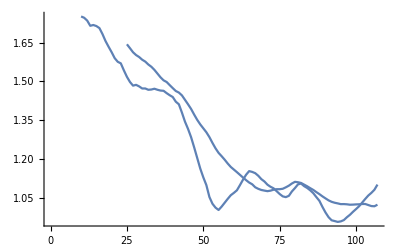

```mathematica
Show[ListLinePlot[ta[[All,4]]],ListLinePlot[ta[[All,5]]]]
```

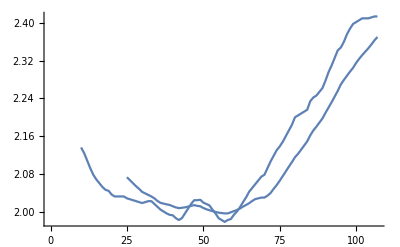

```mathematica
Show[ListLinePlot[ta[[All,7]]],ListLinePlot[ta[[All,8]]]]
```

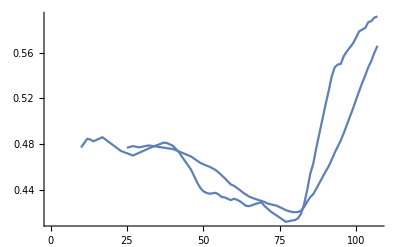

```mathematica
Show[ListLinePlot[ta[[All,10]]],ListLinePlot[ta[[All,11]]]]
```

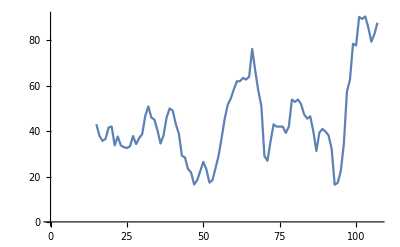

```mathematica
ListLinePlot[ta[[All,19]]]
```

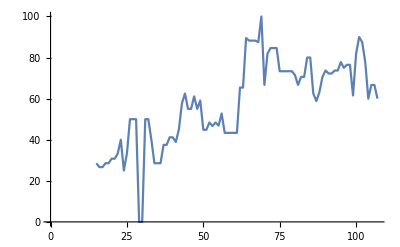

```mathematica
ListLinePlot[ta[[All,27]]]
```

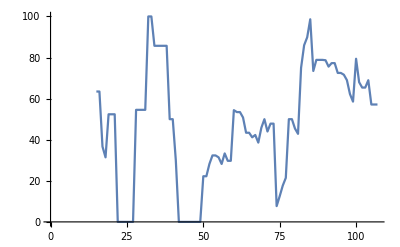

```mathematica
ListLinePlot[ta[[All,35]]]
```

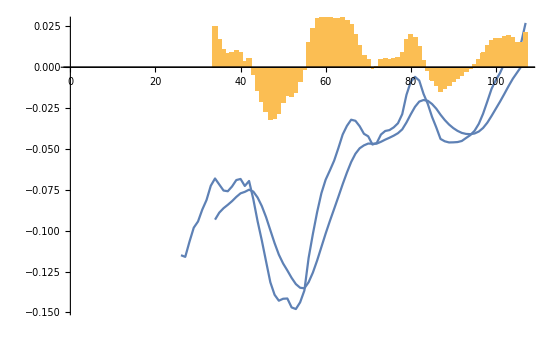

```mathematica
Show[ListLinePlot[ta[[All,39]]],ListLinePlot[ta[[All,40]]],BarChart[ta[[All,41]]]]
```

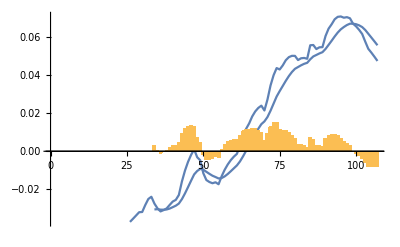

```mathematica
Show[ListLinePlot[ta[[All,45]]],ListLinePlot[ta[[All,46]]],BarChart[ta[[All,47]]]]
```

```mathematica
Show[%277,Background->Directive[RGBColor[0.96,1.,0.9400000000000001],Opacity[1.]]]
```

-Graphics-

```mathematica
Show[%280,AxesStyle->Gray]
```

```mathematica
Show[%277,ImageSize->Full]
```

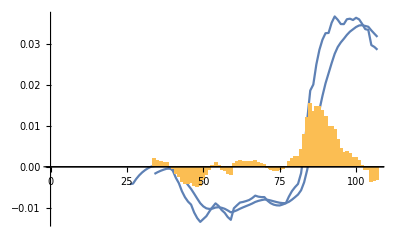

```mathematica
Show[ListLinePlot[ta[[All,51]]],ListLinePlot[ta[[All,52]]],BarChart[ta[[All,53]]]]
```

```mathematica
ultibtbar
```

Statistics  |  Για να δειτε το Xαρτοφυλάκιο  | Efficient Frontier | Portfolios

```mathematica
clear(*Shift+Enter*)
```

```mathematica
Bibliography
```

```mathematica
(n.d.).Retrieved June 11, 2019, from http : // www.helex.gr/el/home

(n.d.).Retrieved June 8, 2019, from http : // www.helex.gr/el/web/guest/stock - company - profile/-/select - stock/252

Brown, K.C., & Frank, R.K.(n.d.).Ανάλυση Επενδύσεων και Διαχείριση Χαρτοφυλακίου.2018 : Broken Hills.

Capital.gr.(n.d.).Αρχική σελίδα.Retrieved June 10, 2019, from http : // www.capital.gr/

Αρχοντάκη, Κ.(2010).Α.Π.Θ.Retrieved June 8, 2019, from http : // ikee.lib.auth.gr/record/123943/files/GRI - 2010 - 5423. pdf

Παπαδάμου, Σ, & Συριόπουλος, Κ.(2015).Βασικές Αρχές Αξιολόγησης Επενδύσεων : Χρηματοοικονομική και Κοινωνικοοικονομική Προσέγγιση.Αθήνα, Ελλάδα : Kalippos.

Μωραϊτόπουλος Π. (2019). Κατασκευή, Ανάλυση και Συγκριτικός Έλεγχος Απόδοσης Μετοχικού Χαρτοφυλακίου Που Επενδύει Στο Ελληνικό Χρηματιστήριο.Βόλος, Ελλάδα: Πανεπιστήμιο Θεσσαλίας, Τμήμα Οικονομικών Επιστημών.

https://reference.wolfram.com/
```